```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

## Global Internal Variables

```mathematica
$DynamicEvaluation
```

False

```mathematica
$HistoryLength=0
```

0

```mathematica
SystemOptions["CacheOptions"]
```

{CacheOptions→{Chemistry→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Date→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Derivative→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Developer→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Geo→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→100000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},GeoFunction→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},GeoTile→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},Image→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→10000000,KeyComparison→None,ResultComparison→LessEqual},NeuralNetworks→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Numeric→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→GreaterEqual},ParametricFunction→{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Quantity→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},Simplify→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Symbolic→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual}}}

```mathematica
MemoryInUse[]
```

573155760

```mathematica
ClearSystemCache[]
```

```mathematica
MemoryInUse[]
```

570377704

#### Memory Debug

From: https://mathematica.stackexchange.com/questions/6177/debugging-memory-leaks

```mathematica
Names["Global`*"]
```

{AEarth,AEarth$,AllbutMassandκFixed,AllbutMassandκFixed$,AllbutMassFixed,AllbutMassFixed$,associationlist,bE,bEarth,bEarth$,bE$,bE$218123,bs,bs$,captured,captured$,CaptureProb,CaptureProb$,context,CoreIndex,CoreIndex$,CrustIndex,CrustIndex$,CrustOrCore,db,db$,dc,dE,dEdlofr,dEdlofr$,directory,directory$,dM,dNcMaxdt,dNcMaxdt$,dσdERoftandω,dσdERoftandω$,dσdERofvχandω,dσdERofvχandω$,EarthVolume,EarthVolume$,eDKEfracchange,eDKEfracchange$,eDvescchange,eDvescchange$,eind,EK,ELAveragede,ELAveragedNuc0,ElectronicσDicst10MeVto1PeV,ElectronicσDicst10MeVto1TeV,ElectronicσDicstallmasses,ElectronicσDicstp1GeV,ElectronicσDicsts,ELfunc,ELfuncTotalbyκsquared,ELfuncTotalbyκsquared$,ELthroughEarthbyκsquared,ELthroughEarthbyκsquared$,ExportToDir,extension,extension$,fD,fDpoints,fDs,fD$,FeTotalparams,FeσDicte10MeVto1PeV,FeσDicte10MeVto1TeV,FeσDicteallmasses,FeσDictemep1GeV,FeσDictNuc10MeVto1PeV,FeσDictNuc10MeVto1TeV,FeσDictNucallmasses,FeσDictNucmep1GeV,fintegrand,fintegrand$,fintegrand$122844,GetCaptureRate,getDefinitions,GetEvaporationRate,GetNc,GetNcMax,GetTotalELFunction,GetvχatEarth,GetvχMax,GetWeakCaptureProbability,GetWeakCaptureProbabilityNuc,GetWeakCaptureTrajectory,h,heavySymbols,h$,i,ICdict,ICdict$,IGCRDict,indexforcapturethreshold,indexforcapturethreshold$,integralofλinvwrtr,integralofλinvwrtrE,integralofλinvwrtrE$,integralofλinvwrtrNuc,integralofλinvwrtrNuc$,integralofλinvwrtr$,Interf,Interf$,InterPDicts,InterPDicts$,InterpolatePc,Intertable,Intertable$,IterateGetCaptureRate,IterateGetEvaporationRate,IterateKEchange,j,k,KEchange,KEchangeDicts,KEchangeDicts$,KEchangeMassDicts,key,k$,l,lDict,ldom,ldom$,list,list$,lowerbrat,lowervrat,lsol,lsol$,ltor,l$,m,mDMtot,meD,meDovermpD,meDovermpD$,meDPoints,meDratio,meDratios,meDratio$,meD$,MgOTotalparams,MgOσDicte10MeVto1PeV,MgOσDicte10MeVto1TeV,MgOσDicteallmasses,MgOσDictemep1GeV,MgσDictNuc10MeVto1PeV,MgσDictNuc10MeVto1TeV,MgσDictNucallmasses,MgσDictNucmep1GeV,mN,mN$,mN$123380,mN$218123,mpD,mpDPoints,mpDPointshigh,mpDPointshigher,mpDPointslow,mpDPointslower,mpD$,mpD$122845,mSMtot,mSMtot$,mχ,mχ$,mχ$122844,mχ$123380,mχ$218123,n,n0,n0$,name,nbs,Nc,NcDict,NcDicts,NcDicts$,NcDict$,NcMax,NcMaxDict,NcMaxDictList,NcMaxDict$,NcMax$,Nc$,nD0,nD0ΛCDM,nD0$,ndups,ndupsmax,ndups$,nT,Ntot,Ntot$,nT$,Nucind,NuclearσDicst10MeVto1PeV,NuclearσDicst10MeVto1TeV,NuclearσDicstallmasses,NuclearσDicstp1GeV,NuclearσDicts,NucleusParams,NucleusParams$,NucleusParams$218123,NucσDict,nvχs,obj,oneminusCDFvmax,oneminusCDFvmax$,OσDictNuc10MeVto1PeV,OσDictNuc10MeVto1TeV,OσDictNucallmasses,OσDictNucmep1GeV,p,params,params$,params$123380,params$218123,path,path$,Pcut,PDict,PDictList,PDictLists,PDictLists$,PDictList$,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10GeVKE,PDicts10GeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1GeVScan,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,pDKEfracchange,pDKEfracchange$,PDom,PDom$,pDvescchange,pDvescchange$,Pfdom,Pfdom$,Pfdom$122844,Pfs,Pfs$,Pfs$122844,Pfunc,PfuncE,PfuncE$,PfuncNuc,PfuncNuc$,Pfunc$,plot,PlotCaptureRateκContour,PlotELfrac,PlotELNucoverE,PlotEvaporationRateκContour,PlotKEchange,PlotKEchangeκContour,plotname,plotname$,PlotNcκContour,PlotPDist,plot$,prop,r,rc,rc$,rE,RE,RegionELDomains,RegionELDomains$,RegionELfuncs,RegionELfuncs$,regionindex,regionindex$,regionindex$218123,RegionVolume,RegionVolume$,RegionΘ,RegionσDicts,RegionσDicts$,rE$,RE$,rE$122844,rootname,rootname$,s,ScanDict,ScanDictList,ScanDictList$,ScanDicts,ScanGetCaptureRateandGetNc,SiO2Totalparams,SiO2σDicte10MeVto1PeV,SiO2σDicte10MeVto1TeV,SiO2σDicteallmasses,SiO2σDictemep1GeV,sizeLim,SiσDictNuc10MeVto1PeV,SiσDictNuc10MeVto1TeV,SiσDictNucallmasses,SiσDictNucmep1GeV,sname,sortedlist,sortedlist$,SortProcessesByRegion,subdirectory,subsubdirectory,SurvivalProb,SurvivalProb$,sym,symbolMemoryUsage,sym$,t,tdom,tdom$,tE,tEarth,tEarth$,tempNcDict,tempNcDict$,tE$,timeenoughforequil,timeenoughforequil$,TrajDict,TrajDict$,V,v0,v0pD,v0pD$,v0Points,v0s,v0toβD,v0$,VCoulombE,VEarth,VEarth$,veDmean,veDmean$,vesc,vesc$,vesc$122844,vfinal,vfinal$,Vgrav,vmax,vmin,vmin$,voft,voft$,vpDmean,vpDmean$,vrEarth,vrEarth$,vT,vχ,vχE,vχmax,vχMax,vχmax$,vχMax$,vχmin,vχmin$,vχmin$218123,vχraw,vχraw$,vχraw$218123,vχs,vχstωcapisωmax,vχstωcapisωmax$,vχs$,vχ$,vχ$218123,y,αD,βD,βD$,βD$122844,βD$122845,βE,βE$,Γevappercapturedparticle,Γevappercapturedparticle$,Γlist,Γlist$,Γtotal,ΓTotal,Γtotal$,ΓTotal$,ΔEfunc,ΔEthroughEarth,ΔEthroughEarth$,Δrbyκsquared,Δrbyκsquared$,ΔrTotbyκsquared,δξ,δξ$,δξ$123380,δξ$218123,κ,κGatheredDicts,κGatheredDicts$,κpoints,κs,κ$,κ$218123,ΛCDMrepl,ΛCDMrepl$,λinvoft,λinvoft$,λinvoft$218123,ξofωandt,ξofωandt$,ξofωandt$218123,ρcritbaumanncm,ρcritbaumanncm$,ρcritbaumannm,ρcritbaumannm$,ρDM0,ρDM0$,σDict,σDictsElectronic,σDictsNuclear,σoftandωmin,σoftandωmin$,σoftandωmin$218123,σofvχandωmin,σofvχandωmin$,χspeedEarth,χspeedEarth$,χtraj,χtraj$,χtraj$218123,ωcapture,ωcapture$,ωcapture$218123,Ωevapperparticle,ΩevapperparticlewvT,ΩevapperparticlewvT$,Ωevapperparticle$,ωmaxoft,ωmaxoft$,ωmaxoft$218123,ωmin,ωmin$,ωmin$123380,ωmin$218123,$globalProperties}

```mathematica
Clear[$globalProperties];
$globalProperties={OwnValues,DownValues,SubValues,UpValues,NValues,FormatValues,Options,DefaultValues,Attributes,Messages};

ClearAll[getDefinitions];
SetAttributes[getDefinitions,HoldAllComplete];
getDefinitions[s_Symbol]:=Flatten@Through[Map[Function[prop,(*Unevaluated needed here just for Options,which is not holding*)Function[sym,prop[Unevaluated@sym],HoldAll]],$globalProperties][Unevaluated[s]]];

ClearAll[symbolMemoryUsage];
symbolMemoryUsage[sname_String]:=ToExpression[sname,InputForm,Function[s,ByteCount[getDefinitions[s]],HoldAllComplete]];

ClearAll[heavySymbols];
heavySymbols[context_,sizeLim_:10^4]:=Pick[#,UnitStep[#-sizeLim]&@Map[symbolMemoryUsage,#],1]&@Names[context<>"*"];
```

```mathematica
heavySymbols["Global`*"]
```

{ElectronicσDicst10MeVto1PeV,FeTotalparams,GetCaptureRate,GetEvaporationRate,MgOTotalparams,NuclearσDicst10MeVto1PeV,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,PlotELfrac,PlotKEchangeκContour,PlotPDist,σoftandωmin$110902}

## Loading and preprocessing

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-1,3}];(*We will scan from 10^-1 GeV to a TeV in increments of 10*) 
mpDPointshigh = mpDPoints[[4;;]];
mpDPointslow = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-3,-2}];(*1 MeV is lowest mass given constraints on ϵ and the fact that we are scanning over meD <= 10^-2 mpD. So at 10 MeV,we run into the red giant cooling bound (since the mass of the lightest species must be above 0.1 MeV)*)


mpDPointshigher = Table["mpD"->10^i 10^12("JpereV")/("c")^2/.SIConstRepl,{i,1,3}];

mpDPointslower = Table["mpD"->10^i 10^6("JpereV")/("c")^2/.SIConstRepl,{i,-2,-1}]; 
(*These values of mpD are ruled out for by stellar cooling bounds, but are the lowest valued meD can be that is consistent with them, hence these values will be used to show capture and evaporation rates for the dark electrons *)
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0

```mathematica
v0Points = {20,220}10^3 ;(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

#### fD

```mathematica
fDpoints = Table[10^i,{i,-3,-1}];
```

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
```

```mathematica
mpDPointslow
```

{mpD→1.78×10^-29}

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

### For Δr

#### Read EL dicts

Nuclear

```mathematica
(*FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];*)
```

Electronic

```mathematica
(*FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];*)
```

### Electronic dσ/dE_R Interpolation Tables

#### 0.1 GeV

```mathematica
FeσDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],FeTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[FeTotalparams]}]
SaveIt[NotebookDirectory[]<>"FeσDictemep1GeV",FeσDictemep1GeV]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictemep1GeV.dat

```mathematica
SiO2σDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True],{i,Length[SiO2Totalparams]}];
SaveIt[NotebookDirectory[]<>"SiO2σDicteme1GeV",SiO2σDictemep1GeV]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01823777020335885790114360816005500964820384979248046875}. NIntegrate obtained 0.00442715 and 9.4584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01833237976527897494793961641335044987499713897705078125}. NIntegrate obtained 0.00442371 and 8.19232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01844268722325083376123444622862734831869602203369140625}. NIntegrate obtained 0.00441968 and 5.60551×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-758.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteme1GeV.dat

```mathematica
MgOσDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],MgOTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[MgOTotalparams]}];
SaveIt[NotebookDirectory[]<>"MgOσDictmep1GeV",MgOσDictemep1GeV]
```

General::munfl: Exp[-726.704] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.706] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.033535219968079676977623648781445808708667755126953125}. NIntegrate obtained 0.0034105 and 6.67258×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.03376852772614136188877864697133190929889678955078125}. NIntegrate obtained 0.00340698 and 6.73205×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.034040546591827369748983755926019512116909027099609375}. NIntegrate obtained 0.00340289 and 6.78681×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictmep1GeV.dat

#### all masses - 0.1 - 10 GeV

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
SaveIt[NotebookDirectory[]<>"FeσDicteallmasses",FeσDicteallmasses]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-734.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853.697] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-992.694] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteallmasses.dat

```mathematica
SiO2σDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]]],{i,Length[SiO2Totalparams]}],{m,3}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDicteallmasses",SiO2σDicteallmasses]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01823777020335885790114360816005500964820384979248046875}. NIntegrate obtained 0.00442715 and 9.4584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01833237976527897494793961641335044987499713897705078125}. NIntegrate obtained 0.00442371 and 8.19232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01844268722325083376123444622862734831869602203369140625}. NIntegrate obtained 0.00441968 and 5.60551×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-758.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteallmasses.dat

```mathematica
MgOσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]]],{i,Length[MgOTotalparams]}],{m,3}],m];
SaveIt[NotebookDirectory[]<>"MgOσDicteallmasses",MgOσDicteallmasses]
```

General::munfl: Exp[-726.704] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.706] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.033535219968079676977623648781445808708667755126953125}. NIntegrate obtained 0.0034105 and 6.67258×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.03376852772614136188877864697133190929889678955078125}. NIntegrate obtained 0.00340698 and 6.73205×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.034040546591827369748983755926019512116909027099609375}. NIntegrate obtained 0.00340289 and 6.78681×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicteallmasses.dat

took about an hour and a half

#### all masses - 100 GeV - 1 TeV

```mathematica
FeσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigh]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighmasses",FeσDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {34.9086}. NIntegrate obtained 4.40938×10^-16 and 4.75294×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {31.3032}. NIntegrate obtained 2.6296×10^-16 and 4.95046×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {36.549}. NIntegrate obtained 1.91727×10^-16 and 6.06913×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-788.674] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916.883] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1066.36] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

Interpolation::inhr: Requested order is too high; order has been reduced to {3,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighmasses.dat

```mathematica
SiO2σDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointshigh]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictehighmasses",SiO2σDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {112.853}. NIntegrate obtained 2.32205×10^-18 and 3.09525×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {91.6305}. NIntegrate obtained 2.3213×10^-18 and 3.07886×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {83.271}. NIntegrate obtained 2.32434×10^-18 and 3.08336×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758.878] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictehighmasses.dat

```mathematica
MgOσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointshigh]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictehighmasses",MgOσDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {103.402}. NIntegrate obtained 1.86302×10^-20 and 2.8856×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {109.266}. NIntegrate obtained 1.88663×10^-20 and 2.68035×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {78.89021024292971606683977370266802608966827392578125}. NIntegrate obtained 1.84517×10^-20 and 3.41541×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-726.911] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.948] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.439] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictehighmasses.dat

took about an hour and a half

#### all masses - 10 MeV and 1 MeV

```mathematica
FeσDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,Length[mpDPointslow]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictelowmasses",FeσDictelowmasses]
```

General::munfl: Exp[-722.545] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-792.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-921.425] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01569}. NIntegrate obtained 0.130635 and 3.06113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01579}. NIntegrate obtained 0.138027 and 3.45634×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01591}. NIntegrate obtained 0.14657 and 4.45193×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictelowmasses.dat

```mathematica
SiO2σDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],False],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointslow]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictelowmasses",SiO2σDictelowmasses]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.726] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.02691}. NIntegrate obtained 0.099083 and 1.44087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00405}. NIntegrate obtained 0.0718564 and 7.34707×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01554}. NIntegrate obtained 0.0378984 and 1.08901×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictelowmasses.dat

```mathematica
MgOσDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,Length[mpDPointslow]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictelowmasses",MgOσDictelowmasses]
```

General::munfl: Exp[-750.045] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.919] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-907.885] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.390983}. NIntegrate obtained 0.0728087 and 8.02628×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01545}. NIntegrate obtained 0.00282614 and 3.96495×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3.28625}. NIntegrate obtained 0.0000199607 and 2.09287×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictelowmasses.dat

took about an hour and a half

#### all masses - 0.1 MeV and 0.01 MeV - errors not in use

```mathematica
(*FeσDictelowermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslower[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointslower]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictelowermasses",FeσDictelowermasses]*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00144453171545485549963350191404742872691713273525238037109375}. NIntegrate obtained 0.0726905 and 2.25209×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0012269962291645286080708776577097296467400155961513519287109375}. NIntegrate obtained 0.0727664 and 2.43744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00110479892792452363933959624819891587321762926876544952392578125}. NIntegrate obtained 0.0729575 and 1.98318×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-790.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-919.431] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.482] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

2

419201. 6.×10^7

688645.

Interpolation::inhr: Requested order is too high; order has been reduced to {1,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::inumr: The integrand -(0.00144809 Im[1/ϵMNum[(«20»)/(«20»),«20»,«1»,{«1»}]])/(EnergyLoss`Private`z) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.0219348-0.0353024 ⅈ,0.0219348+0. ⅈ}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictelowermasses.dat

```mathematica
(*SiO2σDictelowermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslower[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointslower]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictelowermasses",SiO2σDictelowermasses]*)
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.726] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.02691}. NIntegrate obtained 0.099083 and 1.44087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00405}. NIntegrate obtained 0.0718564 and 7.34707×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01554}. NIntegrate obtained 0.0378984 and 1.08901×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictelowmasses.dat

```mathematica
(*MgOσDictelowermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslower[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointslower]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictelowermasses",MgOσDictelowermasses]*)
```

General::munfl: Exp[-750.045] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.919] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-907.885] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.390983}. NIntegrate obtained 0.0728087 and 8.02628×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01545}. NIntegrate obtained 0.00282614 and 3.96495×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3.28625}. NIntegrate obtained 0.0000199607 and 2.09287×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictelowmasses.dat

took about an hour and a half

#### all masses - 10 TeV - 1 PeV

```mathematica
FeσDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigher]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighermasses",FeσDictehighermasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {288.437}. NIntegrate obtained -2.02141×10^-23 and 4.55151×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {284.151}. NIntegrate obtained 8.42389×10^-24 and 6.05067×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {314.185}. NIntegrate obtained 3.6616×10^-23 and 5.54492×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-791.489] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-920.165] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1070.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

126.978 6.×10^7

322390.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

13.2563 6.×10^7

604550.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

89.8933 6.×10^7

280790.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

63.6396 6.×10^7

967886.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

6

5392.87 6.×10^7

568834.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

17120.1 6.×10^7

448089.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

40.1539 6.×10^7

842993.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

4.19201 6.×10^7

427989.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

28.4268 6.×10^7

760018.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

20.1246 6.×10^7

685211.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

1705.38 6.×10^7

911211.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

6

5413.86 6.×10^7

569940.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

12.6978 6.×10^7

596794.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

1.32563 6.×10^7

302993.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

8.98933 6.×10^7

538052.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

6.36396 6.×10^7

485092.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

539.287 6.×10^7

574935.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

1712.01 6.×10^7

912627.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighermasses.dat

```mathematica
SiO2σDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointshigher]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictehighermasses",SiO2σDictehighermasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {610.298744966497}. NIntegrate obtained 9.58256×10^-23 and 3.54025×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {826.265}. NIntegrate obtained 2.07789×10^-22 and 3.1065×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {948.475}. NIntegrate obtained 2.02918×10^-22 and 3.39686×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.215] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

600.375 6.×10^7

600150.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

600.375 6.×10^7

600150.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

189.855 6.×10^7

378669.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

189.855 6.×10^7

378669.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

60.0375 6.×10^7

951114.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

60.0375 6.×10^7

951114.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictehighermasses.dat

```mathematica
MgOσDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointshigher]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictehighermasses",MgOσDictehighermasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1385.76}. NIntegrate obtained -1.09265×10^-23 and 3.06028×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1151.28}. NIntegrate obtained -1.04643×10^-23 and 3.12952×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {891.305944756990442101596272550523281097412109375}. NIntegrate obtained 4.40502×10^-24 and 3.40471×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-738.383] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-809.323] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-892.033] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictehighermasses.dat

took about an hour and a half

### Nuclear dσ/dE_R Interpolation Tables

#### 0.1 GeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs]
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
(*FeσDictNucmp1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs,SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,FeNucCoeffs,200,200,10^-4,False];*)
```

```mathematica
SiσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],SiNucCoeffs]
```

General::munfl: Exp[-21044.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8329.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24536.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],MgNucCoeffs];
```

General::munfl: Exp[-20392.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1850.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],ONucCoeffs];
```

General::munfl: Exp[-8429.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3400.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1460.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucmep1GeV",FeσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"SiσDictNucmep1GeV",SiσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"MgσDictNucmep1GeV",MgσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"OσDictNucmep1GeV",OσDictNucmep1GeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNucmep1GeV.dat

#### all Masses - 0.1 - 10 GeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[m]],FeNucCoeffs,2,"Fe Nuc"],{m,3}];
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136869}. NIntegrate obtained 2.21554×10^-18 and 3.49684×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136286246278912510920822143134500947780907154083251953125}. NIntegrate obtained 1.15673×10^-18 and 2.15718×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.1368562800407380486422681542535428889095783233642578125}. NIntegrate obtained 5.4853×10^-19 and 1.46996×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
SiσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],SiNucCoeffs],{i,3}];
```

General::munfl: Exp[-21044.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8329.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24536.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.215983}. NIntegrate obtained 4.59224×10^-20 and 6.01886×10^-26 for the integral and error estimates.

σ of ξ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.023065}. NIntegrate obtained 5645.7 and 0.00813157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 85.5897 and 0.00244518 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
MgσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],MgNucCoeffs],{i,3}];
```

General::munfl: Exp[-20392.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1850.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.251518219061822763393809765375408460386097431182861328125}. NIntegrate obtained 8.1405×10^-21 and 2.0187×10^-26 for the integral and error estimates.

σ of ξ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000155189095703624449387562911351068350995774380862712860107421875}. NIntegrate obtained 4843.66 and 0.0260529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00700619}. NIntegrate obtained 75.9227 and 0.000286949 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
OσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],ONucCoeffs],{i,3}];
```

General::munfl: Exp[-8429.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3400.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1460.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00934211}. NIntegrate obtained 59.9371 and 0.000689058 for the integral and error estimates.

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00878469}. NIntegrate obtained 4.85252×10^-20 and 5.58431×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00776743}. NIntegrate obtained 3.75733×10^-20 and 4.80404×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucallmasses",FeσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNucallmasses",SiσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNucallmasses",MgσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"OσDictNucallmasses",OσDictNucallmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNucallmasses.dat

```mathematica
InterσofξTable=Table[{Interpointsvχandξ[[i,j]],("ℏ"/.params)(ωmaxofvχ[Interpointsvχandξ[[i,j]][[1]],mχ,params]-ωmin)Abs[Re[NIntegrate[10^Interdσf[Log10[Interpointsvχandξ[[i,j]][[1]]],Log10[ξ]],{ξ,Interpointsvχandξ[[i,j]][[2]],1-ϵ}]]]},{i,m+1},{j,n}];
```

#### all Masses - 100 GeV - 1 TeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[m]],FeNucCoeffs,2,"Fe Nuc",True,10,60],{m,Length[mpDPointshigh]}];
```

```mathematica
SiσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],SiNucCoeffs,1,"Si Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: Exp[-9.09166×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.59841×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.71391×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 6.07865×10^-21 and 1.64679×10^-25 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0201956}. NIntegrate obtained 22086.6 and 0.063041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 311.491 and 0.00704498 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
MgσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],MgNucCoeffs,1,"Mg Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: Exp[-6.88179×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.24588×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45496×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000917172}. NIntegrate obtained 9.06252×10^-21 and 1.85197×10^-25 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 353.218 and 0.00734688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000914281}. NIntegrate obtained 2.73685 and 0.00178775 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],ONucCoeffs,1,"O Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: Exp[-1.44014×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.81026×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.49489×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 2.04384×10^-20 and 6.45361×10^-26 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000155189095703624449387562911351068350995774380862712860107421875}. NIntegrate obtained 486.522 and 0.00228458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00184776}. NIntegrate obtained 5.83453 and 0.000164042 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuchighmasses",FeσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuchighmasses",SiσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuchighmasses",MgσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"OσDictNuchighmasses",OσDictNuchighmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuchighmasses.dat

#### all Masses - 10 MeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[m]],FeNucCoeffs,2,"Fe Nuc",False],{m,Length[mpDPointslow]}];
```

General::munfl: Exp[-794.418] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-926.222] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1079.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0001560797874859855198883575033708126511555747129023075103759765625}. NIntegrate obtained 9.68831×10^16 and 1.63184×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.63012×10^16 and 1.91558×10^10 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0001560797874859855198883575033708126511555747129023075103759765625}. NIntegrate obtained 9.68831×10^16 and 1.63184×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],SiNucCoeffs,1,"Si Nuc",False],{i,Length[mpDPointslow]}];
```

General::munfl: Exp[-724.001] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-844.121] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-984.172] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 3.34182×10^16 and 1.84051×10^11 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 3.34182×10^16 and 1.84051×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00093375}. NIntegrate obtained 3.3417×10^16 and 1.66472×10^11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],MgNucCoeffs,1,"Mg Nuc",False],{i,Length[mpDPointslow]}];
```

General::munfl: Exp[-818.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-954.854] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1113.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00133229}. NIntegrate obtained 2.06691×10^16 and 5.39632×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000237733}. NIntegrate obtained 3.48866×10^15 and 3.95472×10^9 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00133229}. NIntegrate obtained 2.06691×10^16 and 5.39632×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],ONucCoeffs,1,"O Nuc",False],{i,Length[mpDPointslow]}];
```

General::munfl: Exp[-732.545] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854.084] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-995.787] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 2.24553×10^15 and 1.81435×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000237733}. NIntegrate obtained 3.78428×10^14 and 4.49162×10^8 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 2.24553×10^15 and 1.81435×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuclowmasses",FeσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuclowmasses",SiσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuclowmasses",MgσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"OσDictNuclowmasses",OσDictNuclowmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuclowmasses.dat

#### all Masses - 10 TeV - 1 PeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[m]],FeNucCoeffs,2,"Fe Nuc",True,10,60],{m,Length[mpDPointshigher]}];
```

General::munfl: Exp[-5.38669×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.07575×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.3359×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000237733}. NIntegrate obtained 1.08806×10^-23 and 8.65622×10^-27 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 5010.4 and 0.0310652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000381512}. NIntegrate obtained 0.00887386 and 1.76252×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],SiNucCoeffs,1,"Si Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: Exp[-1.43845×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69325×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.29384×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.32199×10^-18 and 3.27836×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000380795}. NIntegrate obtained 1.22607×10^-21 and 3.92166×10^-26 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0018546}. NIntegrate obtained 149.73 and 0.000507645 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

```mathematica
MgσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],MgNucCoeffs,1,"Mg Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: Exp[-1.02611×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.31294×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.66047×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 2.65213×10^-21 and 1.26954×10^-25 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 193.208 and 0.0029423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000914281}. NIntegrate obtained 1.08698 and 0.000218397 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],ONucCoeffs,1,"O Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: Exp[-1.89632×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.65072×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.28517×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.02971×10^-20 and 1.64852×10^-26 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00934211}. NIntegrate obtained 334.633 and 0.00610012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00184776}. NIntegrate obtained 3.61172 and 0.000485638 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuchighermasses",FeσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuchighermasses",SiσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuchighermasses",MgσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"OσDictNuchighermasses",OσDictNuchighermasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuchighermasses.dat

### Combine tables

#### 0.1 GeV

```mathematica
FeσDictemep1GeV=ReadIt[NotebookDirectory[]<>"FeσDictemep1GeV"]
SiO2σDictemep1GeV=ReadIt[NotebookDirectory[]<>"SiO2σDicteme1GeV"]
MgOσDictemep1GeV=ReadIt[NotebookDirectory[]<>"MgOσDictmep1GeV"]
```

```mathematica
FeσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"FeσDictNucmep1GeV"]
SiσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"SiσDictNucmep1GeV"]
MgσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"MgσDictNucmep1GeV"]
OσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"OσDictNucmep1GeV"]
```

```mathematica
(*ElectronicσDicstp1GeV=Join[FeσDictemep1GeV,SiO2σDictemep1GeV,MgOσDictemep1GeV]
NuclearσDicstp1GeV=Join[{FeσDictNucmep1GeV},{SiσDictNucmep1GeV},{MgσDictNucmep1GeV},{OσDictNucmep1GeV}]*)
```

```mathematica
(*Clear[ElectronicσDicstp1GeV,NuclearσDicstp1GeV]*)
```

```mathematica
Clear[FeσDictemep1GeV,SiO2σDictemep1GeV,MgOσDictemep1GeV,FeσDictNucmep1GeV,SiσDictNucmep1GeV,MgσDictNucmep1GeV,OσDictNucmep1GeV]
```

#### all masses - 0.1 - 10 GeV

```mathematica
FeσDicteallmasses=ReadIt[NotebookDirectory[]<>"FeσDicteallmasses"]
SiO2σDicteallmasses=ReadIt[NotebookDirectory[]<>"SiO2σDicteallmasses"]
MgOσDicteallmasses=ReadIt[NotebookDirectory[]<>"MgOσDicteallmasses"]
```

```mathematica
FeσDictNucallmasses=ReadIt[NotebookDirectory[]<>"FeσDictNucallmasses"]
SiσDictNucallmasses=ReadIt[NotebookDirectory[]<>"SiσDictNucallmasses"]
MgσDictNucallmasses=ReadIt[NotebookDirectory[]<>"MgσDictNucallmasses"]
OσDictNucallmasses=ReadIt[NotebookDirectory[]<>"OσDictNucallmasses"]
```

```mathematica
(*ElectronicσDicstallmasses=Table[Join[FeσDicteallmasses[[i]],SiO2σDicteallmasses[[i]],MgOσDicteallmasses[[i]]],{i,3}]
NuclearσDicstallmasses=Table[Join[{FeσDictNucallmasses[[i]]},{SiσDictNucallmasses[[i]]},{MgσDictNucallmasses[[i]]},{OσDictNucallmasses[[i]]}],{i,3}]*)
```

```mathematica
(*ClearAll[ElectronicσDicstallmasses,NuclearσDicstallmasses]*)
```

#### all masses - 10 MeV - 1 TeV

```mathematica
(*FeσDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"];
SiO2σDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"];
FeσDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"]*)
```

```mathematica
FeσDicte10MeVto1TeV=Join[FeσDictelowmasses,FeσDicteallmasses,FeσDictehighmasses];
```

```mathematica
SiO2σDicte10MeVto1TeV=Join[SiO2σDictelowmasses,SiO2σDicteallmasses,SiO2σDictehighmasses]
MgOσDicte10MeVto1TeV=Join[MgOσDictelowmasses,MgOσDicteallmasses,MgOσDictehighmasses]
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDict10MeVto1TeV",FeσDicte10MeVto1TeV]
SaveIt[NotebookDirectory[]<>"SiO2σDict10MeVto1TeV",SiO2σDicte10MeVto1TeV]
SaveIt[NotebookDirectory[]<>"MgOσDict10MeVto1TeV",MgOσDicte10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDict10MeVto1TeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDict10MeVto1TeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDict10MeVto1TeV.dat

```mathematica
FeσDictNuc10MeVto1TeV=Join[FeσDictNuclowmasses,FeσDictNucallmasses,FeσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1TeV",FeσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc10MeVto1TeV.dat

```mathematica
SiσDictNuc10MeVto1TeV=Join[SiσDictNuclowmasses,SiσDictNucallmasses,SiσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1TeV",SiσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc10MeVto1TeV.dat

```mathematica
MgσDictNuc10MeVto1TeV=Join[MgσDictNuclowmasses,MgσDictNucallmasses,MgσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1TeV",MgσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc10MeVto1TeV.dat

```mathematica
OσDictNuc10MeVto1TeV=Join[OσDictNuclowmasses,OσDictNucallmasses,OσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"OσDictNuc10MeVto1TeV",OσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc10MeVto1TeV.dat

```mathematica
FeσDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"FeσDict10MeVto1TeV"]
SiO2σDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"SiO2σDict10MeVto1TeV"]
MgOσDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"MgOσDict10MeVto1TeV"]
```

```mathematica
FeσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1TeV"]
SiσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1TeV"]
MgσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1TeV"]
OσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"OσDictNuc10MeVto1TeV"]
```

```mathematica
(*Clear[ElectronicσDicst10MeVto1TeV,NuclearσDicst10MeVto1TeV]
ElectronicσDicst10MeVto1TeV=Gather[Flatten@Join[FeσDicte10MeVto1TeV,SiO2σDicte10MeVto1TeV,MgOσDicte10MeVto1TeV],#1["mχ"]==#2["mχ"]&];
NuclearσDicst10MeVto1TeV=Gather[Flatten@Join[{FeσDictNuc10MeVto1TeV},{SiσDictNuc10MeVto1TeV},{MgσDictNuc10MeVto1TeV},{OσDictNuc10MeVto1TeV}],#1["mχ"]==#2["mχ"]&];*)
```

```mathematica
(*Clear[ElectronicσDicst10MeVto1TeV,NuclearσDicst10MeVto1TeV]*)
```

```mathematica
"mχ"/.NuclearσDicst10MeVto1TeV
```

{{1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30},{1.78×10^-29,1.78×10^-29,1.78×10^-29,1.78×10^-29},{1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28},{1.78×10^-27,1.78×10^-27,1.78×10^-27,1.78×10^-27},{1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26},{1.78×10^-25,1.78×10^-25,1.78×10^-25},{1.78×10^-24,1.78×10^-24,1.78×10^-24}}

```mathematica
Clear[FeσDicteallmasses,SiO2σDicteallmasses,MgOσDicteallmasses,FeσDictNucallmasses,SiσDictNucallmasses,MgσDictNucallmasses,OσDictNucallmasses]
```

#### all masses - 10 MeV - 1 PeV

```mathematica
FeσDicte10MeVto1PeV=Join[FeσDicte10MeVto1TeV,FeσDictehighermasses];
SiO2σDicte10MeVto1PeV=Join[SiO2σDicte10MeVto1TeV,SiO2σDictehighermasses];
MgOσDicte10MeVto1PeV=Join[MgOσDicte10MeVto1TeV,MgOσDictehighermasses];
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDict10MeVto1PeV",FeσDicte10MeVto1PeV]
SaveIt[NotebookDirectory[]<>"SiO2σDict10MeVto1PeV",SiO2σDicte10MeVto1PeV]
SaveIt[NotebookDirectory[]<>"MgOσDict10MeVto1PeV",MgOσDicte10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDict10MeVto1PeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDict10MeVto1PeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDict10MeVto1PeV.dat

```mathematica
FeσDictNuc10MeVto1PeV=Join[FeσDictNuc10MeVto1TeV,FeσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1PeV",FeσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc10MeVto1PeV.dat

```mathematica
SiσDictNuc10MeVto1PeV=Join[SiσDictNuc10MeVto1TeV,SiσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1PeV",SiσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc10MeVto1PeV.dat

```mathematica
MgσDictNuc10MeVto1PeV=Join[MgσDictNuc10MeVto1TeV,MgσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1PeV",MgσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc10MeVto1PeV.dat

```mathematica
OσDictNuc10MeVto1PeV=Join[OσDictNuc10MeVto1TeV,OσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"OσDictNuc10MeVto1PeV",OσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc10MeVto1PeV.dat

```mathematica
FeσDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"FeσDict10MeVto1PeV"]
SiO2σDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"SiO2σDict10MeVto1PeV"]
MgOσDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"MgOσDict10MeVto1PeV"]
```

```mathematica
FeσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1PeV"]
SiσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1PeV"]
MgσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1PeV"]
OσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"OσDictNuc10MeVto1PeV"]
```

```mathematica
Clear[FeσDicte10MeVto1TeV,SiO2σDicte10MeVto1TeV,MgOσDicte10MeVto1TeV,FeσDictNuc10MeVto1TeV,SiσDictNuc10MeVto1TeV,MgσDictNuc10MeVto1TeV,OσDictNuc10MeVto1TeV]
```

#### Total Combined Dicts

```mathematica
Clear[ElectronicσDicst10MeVto1PeV,NuclearσDicst10MeVto1PeV]
ElectronicσDicst10MeVto1PeV=Gather[Flatten@Join[FeσDicte10MeVto1PeV,SiO2σDicte10MeVto1PeV,MgOσDicte10MeVto1PeV],#1["mχ"]==#2["mχ"]&];
NuclearσDicst10MeVto1PeV=Gather[Flatten@Join[{FeσDictNuc10MeVto1PeV},{SiσDictNuc10MeVto1PeV},{MgσDictNuc10MeVto1PeV},{OσDictNuc10MeVto1PeV}],#1["mχ"]==#2["mχ"]&];
```

```mathematica
Clear[FeσDicte10MeVto1PeV,SiO2σDicte10MeVto1PeV,MgOσDicte10MeVto1PeV,FeσDictNuc10MeVto1PeV,SiσDictNuc10MeVto1PeV,MgσDictNuc10MeVto1PeV,OσDictNuc10MeVto1PeV]
```

### Load Scans

#### From MC

```mathematica
Clear[PDicts1MeVScan]
```

```mathematica
PDicts1MeVScan=ReadIt[NotebookDirectory[]<>"PDicts1MeVScan"];
PDicts10MeVScan=ReadIt[NotebookDirectory[]<>"PDicts10MeVScan"];
PDictsp1GeVScan=ReadIt[NotebookDirectory[]<>"PDictsp1GeVScan"];
PDicts1GeVScan=ReadIt[NotebookDirectory[]<>"PDicts1GeVScan"];
PDicts10GeVScan=ReadIt[NotebookDirectory[]<>"PDicts10GeVScan"];
PDicts100GeVScan=ReadIt[NotebookDirectory[]<>"PDicts100GeVScan"];
PDicts1TeVScan=ReadIt[NotebookDirectory[]<>"PDicts1TeVScan"];
PDicts10TeVScan=ReadIt[NotebookDirectory[]<>"PDicts10TeVScan"];
PDicts100TeVScan=ReadIt[NotebookDirectory[]<>"PDicts100TeVScan"];
PDicts1PeVScan=ReadIt[NotebookDirectory[]<>"PDicts1PeVScan"];
```

#### Get KE Changes

```mathematica
PDicts1MeVKE=IterateKEchange[Flatten@PDicts1MeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10MeVKE=IterateKEchange[Flatten@PDicts10MeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDictsp1GeVKE=IterateKEchange[Flatten@PDictsp1GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1GeVKE=IterateKEchange[Flatten@PDicts1GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10GeVKE=IterateKEchange[Flatten@PDicts10GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts100GeVKE=IterateKEchange[Flatten@PDicts100GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1TeVKE=IterateKEchange[Flatten@PDicts1TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10TeVKE=IterateKEchange[Flatten@PDicts10TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts100TeVKE=IterateKEchange[Flatten@PDicts100TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1PeVKE=IterateKEchange[Flatten@PDicts1PeVScan,{0.05},"α"/.Constants`SIConstRepl];
```

## Definitions

### Utilities

#### Convert from v0 to βD

```mathematica
Clear[v0toβD]
v0toβD[v0_,meD_,mpD_]:=Module[{βD,vpDmean,veDmean},
(*
v0 is the velocity corresponding to the temperature of the aDM particles. By equipartition: 3 Subscript[T, D] = 1/2(Subscript[m, Subscript[e, D]] Subscript[v^2, Subscript[e, D]]+Subscript[m, Subscript[p, D]] Subscript[v^2, Subscript[p, D]]) so we define 3 Subscript[T, D] = m̄ Subscript[v^2, 0] 
*)
βD = 6/((meD + mpD)v0^2);
vpDmean = √(3/(mpD βD));
veDmean = √(3/(meD βD)); 

<|"βD"->βD,"v0"->v0,"vpDmean"->vpDmean,"veDmean"->veDmean|>
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

```mathematica
Clear[RegionΘ]
RegionΘ[r_,regionindex_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{1,r<("rcore"/.Constants`EarthRepl)},{1,r>("rE"/.Constants`EarthRepl)}}[[regionindex;;regionindex]],0]
```

```mathematica
ltor[l_,bE_]:=√(bE^2+l^2)
```

#### Export to Directory

```mathematica
Clear[ExportToDir]
ExportToDir[obj_,name_,subsubdirectory_:"subsubdirectory",subdirectory_:DateString[{"Day","_","Month","_","Year"}],ndupsmax_:500]:=Module[{directory,rootname,extension,path,ndups},
directory=NotebookDirectory[]<>"Plots/"<>subdirectory<>"/"<>subsubdirectory;
{rootname,extension}=StringSplit[name,"."];

If[!DirectoryQ[directory],CreateDirectory[directory]];

ndups=0;
path=directory<>"/"<>rootname<>"_"<>ToString[#]<>"."<>extension&;
While[FileExistsQ[path[ndups]]&&ndups<=ndupsmax,
ndups++;
];

If[(ndups<ndupsmax),Export[path[ndups],obj];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];

]
```

#### Plot P_cap

```mathematica
(*Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]*)
```

```mathematica
Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0,plot},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
(*Print[mpD];
Print[v0];*)
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];
ExportToDir[plot,"Pcap_total.png","Pcap_total"];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];
ExportToDir[plot,"Pcap_electronic.png","Pcap_electronic"];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];
ExportToDir[plot,"Pcap_nuclear.png","Pcap_nuclear"];

ClearAll[Pfunc,plot];
,{p,Length[Pfs]}];
Clear[Pfs];
]
```

```mathematica
(*Clear[PlotPDistEvsNuc]
PlotPDistEvsNuc[PDict_]:=Module[{Pfunc,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
(*Print[mpD];
Print[v0];
PfEs=InterpolatePc[PDict];*)
Do[
Pfunc="PfE"/.PDict[[p]];
κ="κ"/.PDict[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ","Log_10b_E"},PlotLabel->"P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[PDict]}];

Do[
Pfunc="PfNuc"/.PDict[[p]];
κ="κ"/.PDict[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ","Log_10b_E"},PlotLabel->"P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[PDict]}]

]*)
```

#### Plot KE change

```mathematica
Clear[PlotKEchange]
PlotKEchange[KEchangeMassDicts_]:=Module[{AllbutMassFixed,κ,v0,fD,meDovermpD,plotname},
Do[
AllbutMassFixed=Table[KEchangeMassDicts[[i,j]],{i,Length[KEchangeMassDicts]}];
κ=Union["κ"/.AllbutMassFixed][[1]];

If[κ<10^-7,
v0=Union["v0"/.AllbutMassFixed][[1]];
fD=Union["fD"/.AllbutMassFixed][[1]];
meDovermpD=Union["meD"/.AllbutMassFixed][[1]]/Union["mpD"/.AllbutMassFixed][[1]];

(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);*)
plotname=("Δv_e/((v̄)_e)√((α 0.05)/α_D) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListLinePlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"ΔeKE/vpbar"}/.AllbutMassFixed,AxesLabel->{"Log_10mpD [eV]"},PlotLabel->plotname]];
];
,{j,Dimensions[KEchangeMassDicts][[2]]}];
]
```

```mathematica
Clear[PlotKEchangeκContour]
PlotKEchangeκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];
(*Print[meDovermpD];
Print[v0];*)
(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10FractionBox[SubscriptBox[m,SubscriptBox[e,D]],m_p_D\]="<>ToString[Log10@meDovermpD]);*)
plotname=("Log_10Δv_e/((v̄)_e)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]]]];

Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False]}]];

plotname=("Log_10Δv_p/((v̄)_p)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);
Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False]}]]
,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot other parameters

```mathematica
Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];
(*Print[meDovermpD];
Print[v0];*)
(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10FractionBox[SubscriptBox[m,SubscriptBox[e,D]],m_p_D\]="<>ToString[Log10@meDovermpD]);*)
plotname=("Log_10N_c0.05/f_D [ ]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Nc"->(AllbutMassandκFixed[[l,k]]["Nc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
Clear[PlotCaptureRateκContour]
PlotCaptureRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Γ_capn_aDM0.05/f_D [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;
(*Print[VEarth];*)

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"dNcMaxdt"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"dNcMaxdt"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]}]];

(*Print[ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];*)

(*list ={Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]];
Print[Show[{ListDensityPlot[list,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[list,ContourLabels->All,ContourShading->None,Contours->5,ContourStyle->Black]}]];*)

(*Print[ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]];*)

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
Clear[PlotEvaporationRateκContour]
PlotEvaporationRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Γ_evap [s^-1]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

(*Print[ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];*)
Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Γtotal"->(AllbutMassandκFixed[[l,k]]["Γtotal"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
(*Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("N_c0.05/f_D []- "<>" v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=(4π)/3("rE")^3/.Constants`EarthRepl;
Print[VEarth];
Print[ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Nc"]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]*)
```

#### Plot Energy Fraction of Energy Lost

```mathematica
(*Clear[PlotELfrac]
PlotELfrac[PDict_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
Pfunc=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Nuclear*)
Pfunc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]*)
```

```mathematica
Clear[PlotELfrac]
PlotELfrac[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
(*Pfunc=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;*)
Pfunc=κ^2(GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];


(*Nuclear*)
(*Pfunc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;*)
Pfunc=κ^2(GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]
```

```mathematica
(*Clear[PlotELNucoverE]
PlotELNucoverE[PDict_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

PfuncE=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
PfuncNuc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]*)
```

```mathematica
Clear[PlotELNucoverE]
PlotELNucoverE[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*PfuncE=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
PfuncNuc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;*)
PfuncE=κ^2(GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])&;
PfuncNuc=κ^2(GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])&;

(*Print[PfuncE[10^6,10^4]];
Print[PfuncNuc[10^6,10^4]];*)
(*Print[Show[{DensityPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];*)
Print[Show[{DensityPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]
```

### MC Processes

#### Gravitational Potential

```mathematica
Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("ME" "G")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

#### Select Interaction Process

```mathematica
(*σselector[σs_]:=Module[{ξ2,Ps,Psums,Nσ,n},

ξ2 = Random[];

Nσ=Length[σs];
Ps=σs/Total[σs];
Psums=Table[Sum[Ps[[i]],{i,j}],{j,Length[Ps]}];

n=0;
Do[If[ ξ2<=Psums[[i]],n=i;Break[]],{i,1,Nσ}];
(*{n,ξ2,N[Psums]}*)
n
]*)
```

#### EL and Δr total

```mathematica
(*Clear[ELEarthTot]

fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl 

fNuc0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)

fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] ]
fNuc0ELCore[mχ_,vχ_]:=Log10[10^FeNuc0ELDict[["f"]][mχ,vχ]]

ELEarthTot[r_,mχ_,vχ_]:=Piecewise[{{10^fTot0ELMantle[Log10[mχ], Log10[vχ]],("rE"/.Constants`EarthRepl)> r >=  ("rcore"/.Constants`EarthRepl)},{10^fTot0ELCore[Log10[mχ], Log10[vχ]], ("rcore"/.Constants`EarthRepl)>r}},0]*)
```

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
(*Clear[ΔrAveragedTot0,ΔETot0]

ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)

ΔEe[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]])) /.consts ]]

ΔENuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fNuc0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)
EK[mχ_,vχ_] :=1/2 mχ vχ^2
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl,y_:10^-2]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]

ELAveragede[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl]:=  EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]

ELAveragedNuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl]:=EK[mχ,vχ]/ΔENuc0[mχ,vχ,κ,bE,consts]

fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]*)
```

```mathematica
(*Clear[GetTotalELFunction]
GetTotalELFunction[ElectronicσDicsts_,NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts,NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

(*Returns: dEdl[r,vχ]*)
Quiet@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],("rE"/.Constants`EarthRepl)> #1 >=  ("rcore"/.Constants`EarthRepl)},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], ("rcore"/.Constants`EarthRepl)>#1}},0]&
]*)
```

```mathematica
Clear[GetTotalELFunction]
GetTotalELFunction[ElectronicσDicsts_,NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts,NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
(*ΔEthroughEarth=Quiet@Re@Piecewise[{{("JpereV"/.Constants`SIConstRepl)(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{("JpereV"/.Constants`SIConstRepl)dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GeteELFunction]
GeteELFunction[ElectronicσDicsts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
(*ΔEthroughEarth=Quiet@Re@Piecewise[{{("JpereV"/.Constants`SIConstRepl)(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{("JpereV"/.Constants`SIConstRepl)dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GetNucELFunction]
GetNucELFunction[NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
(*ΔEthroughEarth=Quiet@Re@Piecewise[{{("JpereV"/.Constants`SIConstRepl)(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{("JpereV"/.Constants`SIConstRepl)dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔrTotbyκsquared[mχ_,vχ_,bE_,ΔEfunc_,y_:10^-2]:=Re[dE[bE] y EK[mχ,vχ]/ΔEfunc[bE,vχ] ]
```

#### Weak Capture Regime Trajectory

```mathematica
(*Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_]:=Module[{RE,lsol,ldom,voft},
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχELEarthTot[√(bE^2+l[t]^2),mχ,l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]*)
```

```mathematica
Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,lsol,ldom,voft},
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχ ELfunc[√(bE^2+l[t]^2),l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

#### Weak Capture Regime Capture Probability

```mathematica
Clear[GetWeakCaptureProbability]
GetWeakCaptureProbability[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,tdom,κ,regionindex,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr,SurvivalProb,CaptureProb},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;
κ=("κ"/.lDict);
regionindex = "regionindex"/.σDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;
χtraj=("l(t)"/.lDict);
bE=("bE"/.lDict);(*impact parameter*)

ξofωandt=Abs[EnergyLoss`ξofωandvχ[#1,ωmin,("v(t)"/.lDict)[#2],mχ,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxofvχ[("v(t)"/.lDict)[#1],mχ,params]&;

dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]])&;

(*Print[("σofξf"/.σDict)[4,Log10[0.1]]];*)

(*
(*Pre ωcapture*)
σoft=If[vχraw[#]>vχmin,("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωmin,ωmaxoft[#]}],0]&;(* ℏ from the jacobians Subscript[E, R]->ω *)
*)

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl))&;

(*Print[ωcapture[50]];*)
(*ω needed to have v < vesc*)
(*σoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωcapture[#],ωmaxoft[#]}],0]&;*)(* ℏ from the jacobians Subscript[E, R]->ω *)

λinvoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;

(*Print[("κ"/.lDict)];
Print[("ne"/.params)];*)

(*Print[Log10@vχ[50]];
Print[Log10@ξofωandt[#2,#1]]&[50,ωcapture[50]];
Print[("σofξf"/.σDict)[Log10@vχ[50],Log10@ξofωandt[#2,#1]&[50,ωcapture[50]]]];
Print[("σofξf"/.σDict)[4,Log10[0.1]]];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]]*)
(*Print[("σofξf"/.σDict)];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]];*)
(*Print[λinvoft];
Print[σoftandωmin[#,ωcapture[#]]&[50]];
Print[(("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]])&[50,ωcapture[50]]];
Print[("σofξf"/.σDict)];*)
(*Print[Plot[λinvoft[t]/(("κ"/.lDict)^2("ne"/.params)),{t,tdom[[1]],tdom[[2]]}]];
Print[Plot[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}]];*)

(*Print["tdom is ",Round[tdom[[2]]]];
Print[λinvoft[50]vχ[50]];*)

(*integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];*)
integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t]RegionΘ[ltor[χtraj[t],bE],regionindex],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];

(*integralofλinvwrtr=NIntegrate[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)
(* vχ from the jacobians l -> t - do simple numerical integral here, Nintegrate was giving some weird divergin issues*)
(*SurvivalProb =E^-integralofλinvwrtr;
CaptureProb=1-SurvivalProb;*)

(*Print[integralofλinvwrtr];*)
(*Print["Starting Nintegrate"];
Print@NIntegrate[σoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)

(*<|"SurvivalProb"->SurvivalProb,"CaptureProb"->CaptureProb|>*)
integralofλinvwrtr
]
```

-Graphics-

We run into this issue when we try to use NIntegrate for the survival probability integral

```mathematica
Clear[GetWeakCaptureProbabilityNuc]
GetWeakCaptureProbabilityNuc[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,tdom,κ,regionindex,mN,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;
κ=("κ"/.lDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;

(*Print[mN];*)

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;

χtraj=("l(t)"/.lDict);
bE=("bE"/.lDict);(*impact parameter*)

ξofωandt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,("v(t)"/.lDict)[#2],mχ,mN,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxNuc[("v(t)"/.lDict)[#1],mχ,mN,params]&;

dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]])&;

(*Print[("σofξf"/.σDict)[4,Log10[0.1]]];*)

(*
(*Pre ωcapture*)
σoft=If[vχraw[#]>vχmin,("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωmin,ωmaxoft[#]}],0]&;(* ℏ from the jacobians Subscript[E, R]->ω *)
*)

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl))&;

(*Print[ωcapture[50]];*)
(*ω needed to have v < vesc*)
(*σoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωcapture[#],ωmaxoft[#]}],0]&;*)(* ℏ from the jacobians Subscript[E, R]->ω *)

λinvoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;

(*Print[("κ"/.lDict)];
Print[("ne"/.params)];*)

(*Print[Log10@vχ[50]];
Print[Log10@ξofωandt[#2,#1]]&[50,ωcapture[50]];
Print[("σofξf"/.σDict)[Log10@vχ[50],Log10@ξofωandt[#2,#1]&[50,ωcapture[50]]]];
Print[("σofξf"/.σDict)[4,Log10[0.1]]];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]]*)
(*Print[("σofξf"/.σDict)];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]];*)
(*Print[λinvoft];
Print[σoftandωmin[#,ωcapture[#]]&[50]];
Print[(("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]])&[50,ωcapture[50]]];
Print[("σofξf"/.σDict)];*)
(*Print[Plot[λinvoft[t]/(("κ"/.lDict)^2("ne"/.params)),{t,tdom[[1]],tdom[[2]]}]];
Print[Plot[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}]];*)

(*Print["tdom is ",Round[tdom[[2]]]];
Print[λinvoft[50]vχ[50]];*)

integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t]RegionΘ[ltor[χtraj[t],bE],regionindex],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];
(*integralofλinvwrtr=NIntegrate[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)
(* vχ from the jacobians l -> t - do simple numerical integral here, Nintegrate was giving some weird divergin issues*)
(*
SurvivalProb =E^-integralofλinvwrtr;
CaptureProb=1-SurvivalProb;*)
(*Print[integralofλinvwrtr];*)
(*Print["Starting Nintegrate"];
Print@NIntegrate[σoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)

(*<|"SurvivalProb"->SurvivalProb,"CaptureProb"->CaptureProb,|>*)
integralofλinvwrtr
]
```

### Initial Conditions

```mathematica
Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_]:=Module[{oneminusCDFvmax,vesc},
vesc=("vesc"/.Constants`EarthRepl);
oneminusCDFvmax = ⅇ^(1/2 mχ vesc^2 βD) (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/(2 π))vmax] );(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmax/.NSolve[{Pcut==oneminusCDFvmax&&0<vmax<10^6},vmax][[1]]
]
```

```mathematica
Integrate[ ⅇ^(-1/2 m (v^2-vesc^2) β) √(2/π) v^2 (m β)^(3/2) ,{v,vmax,∞}]
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[(ⅇ^(1/2 m vesc^2 β) (m β)^(3/2) (2 ⅇ^(-1/2 m vmax^2 β) m vmax β+√(2 π) √(m β)-√m √(2 π) √β Erf[(√m vmax √β)/(√2)]))/(m^2 √(2 π) β^2), Re[m β]>0]

(ⅇ^(1/2 m vesc^2 β) (√(2 π)+2 ⅇ^(-1/2 m vmax^2 β) √m vmax √β-√(2 π) Erf[(√m vmax √β)/(√2)]))/(√(2 π))

```mathematica
(*Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:10,nvχs_:30,lowerbrat_:10^-6]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},



    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
    vχs = 10^Subdivide[Log10@vmin,Log10@vχMax,nvχs];
    (*bs = 10^Subdivide[Log10[lowerbrat rE],Log10@rE,nbs];*)
bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]*)
```

```mathematica
Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:10,nvχs_:30,lowerbrat_:10^-6,lowervrat_:10^-3]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
    (*vχs = 10^Subdivide[Log10@vmin,Log10@vχMax,nvχs];*)
(*Print[10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs]];*)
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];
(*Print[vχs];*)
    (*bs = 10^Subdivide[Log10[lowerbrat rE],Log10@rE,nbs];*)
bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]
```

### Get Capture Probability

New Psuedocode:

pass the initial conditions and κ to get capture rate

```mathematica
Clear[GetCaptureRate]
GetCaptureRate[meDovermpD_,κ_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{mpD,meD,βD,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProb,PDictList={}},

mpD=Join["mχ"/.σDictsElectronic,"mχ"/.σDictsNuclear];
mpD=If[Length@Union[mpD]==1,mpD[[1]],Print["mχ must be the same in all processes:",mpD];Return[<||>,Module]];
meD = meDovermpD mpD;

(*Print@v0toβD[v0,meD,mpD];
*)
βD ="βD"/.v0toβD[ v0,meD,mpD];

vχMax=GetvχMax[10^-6,βD,mpD];
(*Print[vχMax];*)

(*Print[v0];
Print[meDovermpD];*)

ICdict=Flatten@GetvχatEarth[mpD,βD,vχMax];(*dictionary of initial conditions at earth*)

(*Print["χspeedEarth"/.ICdict];*)

{ELfuncTotalbyκsquared,ELthroughEarthbyκsquared} = {"dEdlofr","ΔEthroughEarth"}/.GetTotalELFunction[σDictsElectronic,σDictsNuclear];

(*Print[ICdict];*)
(*Print[ELfuncTotalbyκsquared[10^6,10^6]];
Print[ELthroughEarthbyκsquared[10^6,10^6]];*)

(*Print[ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],1+Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],2+Log10[ "χspeedEarth"]/.ICdict];
(*Print@dM["bEarth"/.ICdict];*)
Print@dc["bEarth"/.ICdict];
Print[("rcore"/.Constants`EarthRepl)>("bEarth"/.ICdict)^2];*)
(*"JpereV"ΔETot0[mpD,"χspeedEarth"/.ICdict,κ,"bEarth"/.ICdict,Constants`SIConstRepl]/.Constants`SIConstRepl*)
Monitor[
Do[
(*Δrbyκsquared=ΔrAveragedTot0[mpD,"χspeedEarth"/.ICdict[[n]],1,"bEarth"/.ICdict[[n]]];*)
Δrbyκsquared=ΔrTotbyκsquared[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared];
RE=dE["bEarth"/.ICdict[[n]]];

(*Print["Δr: ",Δrbyκsquared];*)
(*Print[Δrbyκsquared];*)

(*Print@Δrbyκsquared;*)
(*Print@(Δrbyκsquared/RE);*)
(*κStrongWeakBoundary=κt/.Solve[Δrbyκsquared/κt^2==RE/100,κt][[2]];*)
(*Print[ELEarthTot[r,mpD,"χspeedEarth"/.ICdict]/.r->1/2"rE"/.Constants`EarthRepl];*)
(*Plot[(ELEarthTot[#,mpD,"χspeedEarth"/.ICdict])&[r],{r,1,"rE"/.Constants`EarthRepl}];*)

If[Δrbyκsquared/κ^2>RE/100,

(*TrajDict=GetWeakCaptureTrajectory[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ];*)
TrajDict=GetWeakCaptureTrajectory[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];
(*Print[Plot["l(t)"[t]/.TrajDict,{t,0,TrajDict["domain"][[2]]}]];
Print[Plot["v(t)"[t]/.TrajDict,{t,0,TrajDict["domain"][[2]]}]];
*)
vfinal= ("v(t)"/.TrajDict)[TrajDict["domain"][[2]]];
captured=vfinal<"vesc"/.Constants`EarthRepl;

(*captured=False;*)
(*If[captured,Print["Captured"]];*)

(*σdict = Fe2eDictUnitTest;*)
If[!captured,
integralofλinvwrtrE = Total@Table[GetWeakCaptureProbability[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNuc[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];

Quiet@Clear[vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,tdom,regionindex,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr];
Quiet@Clear[vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,tdom,regionindex,mN,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr];

(*put get NcMax here*)

SurvivalProb =E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc));
CaptureProb=1-SurvivalProb;
AppendTo[PDictList,<|"Psurv"->N@SurvivalProb,"Pcap"->Max[CaptureProb,10^-50],"CSDcap"->captured,"vχE"->"χspeedEarth"/.ICdict[[n]],"bEarth"->("bEarth"/.ICdict[[n]]),"vfinal"->vfinal,"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->Max[1-E^-integralofλinvwrtrE,10^-50],"PcapNuc"->Max[1-E^-integralofλinvwrtrNuc,10^-50],"intλinvE"->integralofλinvwrtrE,"intλinvNuc"->integralofλinvwrtrNuc|>];,
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->vfinal,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->50,"intλinvNuc"->50|>]
];
,
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->0,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->50,"intλinvNuc"->50|>]
];
,{n,Length[ICdict]}
];
,n];
PDictList
]
```

```mathematica
Clear[IterateGetCaptureRate]
IterateGetCaptureRate[meDovermpD_,κs_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{PDictList={}},

Monitor[
Do[Print["κ is: ",N@κs[[κ]]];
Print["Memory before ",ToString[MemoryInUse[]]];PDictList=Join[PDictList,GetCaptureRate[meDovermpD,κs[[κ]],v0,σDictsElectronic,σDictsNuclear]];
Print["Memory after ",ToString[MemoryInUse[]]];,{κ,Length[κs]}];
Quiet@Clear[mpD,meD,βD,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProp];
,κ];

(*NotCSDcaptured = {};
Do[If[!"CSDcap"/.PDictList[[i]],AppendTo[NotCSDcaptured,PDictList[[i]]]],{i,Length[PDictList]}];
*)
(*<|"AllDicts"->PDictList,"NotCSDStopped"->NotCSDcaptured|>*)
(*<|"AllDicts"->PDictList|>*)
PDictList
]
```

```mathematica
Clear[InterpolatePc]
InterpolatePc[PDictList_]:=Module[{Intertable,Interf,κGatheredDicts,mpD,meD,vχMax,βD,v0},

{mpD,meD,vχMax,βD,v0}=Union[{"mpD","meD","vχMax","βD","v0"}/.PDictList][[1]];
(*Print[Union[{"mpD","meD","vχMax","βD","v0"}/.PDictList][[1]]];*)
κGatheredDicts=Gather[PDictList,(#1["κ"]==#2["κ"])&];
Interf=Table[<|"Pf"->Interpolation[Log10@{{"vχE","bEarth"},"Pcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"κ"->(Union["κ"/.κGatheredDicts[[i]]][[1]]),"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"PfE"->Interpolation[Log10@{{"vχE","bEarth"},"PcapE"}/.κGatheredDicts[[i]],InterpolationOrder->1],"PfNuc"->Interpolation[Log10@{{"vχE","bEarth"},"PcapNuc"}/.κGatheredDicts[[i]],InterpolationOrder->1]|>,{i,Length[κGatheredDicts]}];
Interf
]
```

### Get Total Capture Rate

#### Flux and NcMax defn

```mathematica
nD0ΛCDM[fD_,mDMtot_] := Module[{ΛCDMrepl,h,ρcritbaumanncm,ρcritbaumannm, n0,mSMtot,ρDM0},
ΛCDMrepl= {"Ωk" ->0.00,"Ωr"->9.4 10^-5, "Ωm"->0.32,"ΩΛ"->0.68,"Ωb"->0.05,"Ωc"->0.27}; (*[] ΛCDM density parameters*)
h= 0.67; (*baumann 1.2.64*)

ρcritbaumanncm = 1.1 10^-5 h^2; (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  (10^6); (*[protons m^-3]*)

n0 = "Ωb" ρcritbaumannm /.ΛCDMrepl;  (*[m^-3] proton / electron number density today*)
mSMtot= "m" + 2000 "m"/.Constants`SIConstRepl;

ρDM0= "Ωc"/"Ωb" n0 mSMtot/.ΛCDMrepl;
ρDM0/mDMtot fD
]
```

```mathematica
(*GetFluxAtEarth[mχ_,βD_,nD_]:=Module[{},
(*nD is the local aDM number density*)
(ⅇ^(1/4 mχ ("vesc")^2 βD) √mχ nD ("vesc")^2 √βD BesselK[1,1/4 mχ ("vesc")^2 βD])/(2 √(2 π))/.Constants`EarthRepl
]*)
```

```mathematica
(*Clear[GetNcMax]
GetNcMax[Pcapbar_,mχ_,βD_,nD_]:=Module[{tEarth,AEarth,dNcMaxdt,NcMax},
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π ("rE")^2/.Constants`EarthRepl; (*[m^2] Area of the Earth*)
dNcMaxdt = Pcapbar AEarth GetFluxAtEarth[mχ,βD,nD];(*capture rate of aDM*)
NcMax = tEarth dNcMaxdt;
<|"NcMax"->NcMax,"dNcMaxdt"->dNcMaxdt|>
]*)
```

```mathematica
Clear[GetNcMax]
GetNcMax[IGCRDict_]:=Module[{InterPDicts,Pfs,rE,vesc,tEarth,AEarth,mχ,βD,Pfdom,fintegrand,dNcMaxdt,db=10^-4("rE"/.Constants`EarthRepl)},
(*Get maximum possible accumulation over the lifetime of Earth, with κ=1*)

InterPDicts=InterpolatePc[IGCRDict];
Quiet@Clear[Intertable,Interf,κGatheredDicts,mpD,meD,vχMax,v0];
Pfs="Pf"/.InterPDicts;

rE="rE"/.Constants`EarthRepl;
vesc = "vesc"/.Constants`EarthRepl;
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Area of the Earth*)

Do[
mχ="mpD"/.InterPDicts[[i]];
βD="βD"/.InterPDicts[[i]];
Pfdom=Pfs[[i]]["Domain"];
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[NIntegrate[#^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + #^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@#],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}]&[bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[Total@Table[db bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,Round[10^Pfdom[[2,1]]],Round[10^Pfdom[[2,2]]],Round[db]}],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];*)
fintegrand[vχ_?NumberQ]:=NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];
dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];
AppendTo[InterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[InterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];
,{i,Length[Pfs]}];
InterPDicts
]
```

#### Evaporation Rate

```mathematica
Clear[GetEvaporationRate]
GetEvaporationRate[σDict_]:= Module[{vχmin,vχmax,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,ξofωandvχ,ωmaxofvχ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
 
(*Print[mχ("c")^2/("JpereV")/.SIConstRepl];
Print[√(2/(mχ βE))];
Print[1/βE 1/("JpereV")/.SIConstRepl];*)

ξofωandvχ=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]-δξ]&;

(*dσdERofvχandω=10^Re@("dσf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]&;*)

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]])&;

(*vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχmaxofvχ =(2 ("ℏ"/.params))/mχ ωmaxofvχ[#]&;*)
vχmin = 10^(("σofξf"/.σDict)["Domain"][[1,1]]);
(*vχmax=  10^(("σofξf"/.σDict)["Domain"][[1,2]]);*)

(*Post ωcapture*)
ωmaxofvχ=EnergyLoss`ωmaxNuc[#1,mχ,mN,params]&;
(*ωcapture = Max[1/(2 ("ℏ"/.params))mχ (("vesc"/.Constants`EarthRepl)^2-#^2 ),1/(2 ("ℏ"/.params))mχ vχmin^2]&;*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (("vesc"/.Constants`EarthRepl)^2-#^2 )&;(*We are going outside the range of the interpolating function at times. *)

(*Print[Solve[ω==ωmaxofvχ[vχ]]];*)


vχstωcapisωmax=vχ/.NSolve[ωmaxofvχ[vχ]==ωcapture[vχ],vχ][[2]];


ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[vT^2 E^(-βE 1/2 mN vT^2)Total@Table[((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2)HeavisideTheta[ωmaxofvχ[vχ]-ωcapture[vχ]]σofvχandωmin[vχ,ωcapture[vχ]],{vχ,Round[vχstωcapisωmax],Round["vesc"/.Constants`EarthRepl]}],{vT,0,∞}];(*first factor in table comes from integral of |vT - vχ| over cosθ *)


RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}];
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;
(*Print[RegionVolume];*)
Γevappercapturedparticle=ΩevapperparticlewvT RegionVolume/EarthVolume; (*Γκ^2 corresponds to Revp in appendix*)(*Assumes homogeneously distributed aDM in the Earth*)

Γevappercapturedparticle
]
```

```mathematica
Clear[IterateGetEvaporationRate]
IterateGetEvaporationRate[NuclearσDicts_]:=Module[{Γlist={},ΓTotal},
Monitor[
Do[
AppendTo[Γlist,GetEvaporationRate[NuclearσDicts[[n]]]],
{n,Length[NuclearσDicts]}
];
,n];
ΓTotal=Total[Γlist];
<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Get N_c in the presence of evaporation

```mathematica
Clear[GetNc]
GetNc[NcMaxDictList_,NucσDict_]:=Module[{indexforcapturethreshold,κ,NcMax,dNcMaxdt,Γtotal,tE,timeenoughforequil,Nc,tempNcDict={},NcDicts={}},
Γtotal="ΓTotal"/.IterateGetEvaporationRate[NucσDict];(*evaporation rate per captured particle assuming homogeneous distribution in the Earth - Conservative: it is dominated by the core, the lower g there will reduce the number density*)
(*Print[Γtotal];*)
Do[
(*Print[NcMaxDictList[[i]]];*)
NcMax="NcMax"/.NcMaxDictList[[i]];
dNcMaxdt="dNcMaxdt"/.NcMaxDictList[[i]];
tE=NcMax/dNcMaxdt;(*[s] age of the Earth*)

κ="κ"/.NcMaxDictList[[i]];
(*Print[Γtotal];
Print[κcaptures^2 Γtotal ];
Print[(κcaptures^2 Γtotal )[[1]]];
Print[Table[(κcaptures^2 Γtotal )[[i]],{i,Length[κcaptures]}]];*)
timeenoughforequil=1/tE<(κ^2 Γtotal);(*has had time to equilibrate if age of Earth is greater than evaporation time scale*)
(*Print[timeenoughforequil];*)
(*tempNcDict = Append[NcMaxDictList[[i]],<||>];*)
(*Print[NcMaxDictList[[i]]];*)
(*Nc=If[timeenoughforequil,dNcMaxdt/Γtotal,κ^2 NcMax ];*)(*both per particle evaporation and capture rates scale as κ^2, so in equilibirium, the captured number is independent of it ---- WRONG!!!*)
Nc=If[timeenoughforequil,dNcMaxdt/(κ^2 Γtotal),NcMax ];(*both per particle evaporation and capture rates scale as κ^2, so in equilibirium, the captured number is independent of it ---- WRONG!!!*)
(*Print[Nc];*)

tempNcDict = Append[NcMaxDictList[[i]] ,{"timeenoughforequil"->timeenoughforequil,"Nc"->Nc,"Γtotal"->Γtotal}];
AppendTo[NcDicts,tempNcDict];
,{i,Length[NcMaxDictList]}];
NcDicts
]
```

#### Scan parameter space

```mathematica
Clear[ScanGetCaptureRateandGetNc]
ScanGetCaptureRateandGetNc[meDratios_,κs_,v0s_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PDictList,PDictLists={},ScanDictList={},meDratio,v0,mpD,βD,NcMaxDict,NcDict,MemoryUsed={}},
mpD= "mχ"/.ElectronicσDicsts[[1]];
Print["mpD: ",mpD( ("JpereV")/("c")^2)^-1/.Constants`SIConstRepl];
Do[
meDratio=("meD/mpD"/.meDratios[[m]]);
v0 = v0s[[n]];
βD ="βD"/.v0toβD[v0,meDratio mpD,mpD];
Print["meD/mpD: ",meDratio];
Print["v0: ",v0];
Print["βD: ",βD];

AppendTo[MemoryUsed,"Memory before IGCR at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];

PDictList=IterateGetCaptureRate[meDratio,κs,v0,ElectronicσDicsts,NuclearσDicts];
(*AppendTo[PDictLists,PDictList];*)

AppendTo[MemoryUsed,"Memory before Plotting at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];

PlotPDist[PDictList];
Quiet@Clear[Pfunc,Pfs,κ,plot];

AppendTo[MemoryUsed,"Memory before GNM at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];

NcMaxDict=GetNcMax[PDictList];

AppendTo[MemoryUsed,"Memory before GN at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];

NcDict=GetNc[NcMaxDict,NuclearσDicts];

AppendTo[MemoryUsed,"Memory before Clearing at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];

Quiet@Clear[indexforcapturethreshold,κ,NcMax,dNcMaxdt,Γtotal,tE,timeenoughforequil,Nc,tempNcDict,NcDicts];
Quiet@Clear[InterPDicts,Pfs,rE,vesc,tEarth,AEarth,mχ,Pfdom,fintegrand,dNcMaxdt,db];
Quiet@Clear[vχmin,vχmax,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume];

AppendTo[MemoryUsed,"Memory after Clearing at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];

AppendTo[ScanDictList, NcDict];
(*AppendTo[ScanDictList,{v0,meDratio}];*)


Print[MemoryUsed];

(*AppendTo[ScanPointInfoList,<|"Pcaps"->κPtable[[;;,2]],"κs"->κPtable[[;;,1]],"NcMaxes"->("NcMax"/.NcMaxes),"dNcMaxdt"->("dNcMaxdt"/.NcMaxes),"βD"->βD,"v0"->v0,"meD/mpD"->meDratio,"mpD"->mpD|>];*)
,{m,Length[meDratios]},{n,Length[v0s]}];

(*<|"PDictLists"->PDictLists,"ScanDictList"->ScanDictList|>*)
ScanDictList
]
```

### Get Significant Capture Regimes

#### KE Change

```mathematica
VCoulombE[N_,αD_]:=αD/("α")("e")^2/(4 π "ϵ0")N/("rE")/.Constants`EarthRepl/.Constants`SIConstRepl
```

```mathematica
(*Clear[KEchange]
KEchange[NmaxnD0is1_,fD_,αD_,mpD_,meDratio_]:=Module[{Ntot,pDvescchange,eDvescchange},

Ntot = nD0ΛCDM[fD,mpD(1+meDratio)]NmaxnD0is1;
pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/(meDratio mpD));
<|"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"Ntot"->Ntot|>
]*)
```

```mathematica
Clear[KEchange]
KEchange[ScanDict_,fD_,αD_]:=Module[{mpD,meD,nD0,Nc,Ntot,pDvescchange,eDvescchange,pDKEfracchange,eDKEfracchange},
{mpD,meD}={"mpD","meD"}/.ScanDict;
(*Print[mpD," ",meD];*)
nD0=nD0ΛCDM[fD,mpD +meD];

Nc="Nc"/.ScanDict;
Ntot = Nc/."nD"->nD0;

pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/meD);
pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)))/.Constants`EarthRepl/.ScanDict;
(*Print[pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict];*)
Append[ScanDict,{"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"ΔpKE/vpbar"->pDKEfracchange,"ΔeKE/vpbar"->eDKEfracchange,"Ntot"->Ntot,"nD"->nD0,"fD"->fD,"αD"->αD}]
]
```

```mathematica
Clear[IterateKEchange]
IterateKEchange[ScanDicts_,fDs_,αD_]:=Module[{KEchangeDicts={}},
Do[
AppendTo[KEchangeDicts,KEchange[ScanDicts[[i]],fDs[[j]],αD]];
,{i,Length[ScanDicts]},{j,Length[fDs]}];
KEchangeDicts
]
```

## Run

#### Scan over the masses 1 MeV - 1 GeV

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1MeVScan",PDicts1MeVScan]
Clear[PDicts1MeVScan]
```

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10MeVScan",PDicts10MeVScan]
Clear[PDicts10MeVScan]
```

2

2

mpD: 1.×10^7

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

Memory before 504018152

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 510203128

κ is: 1.×10^-13

Memory before 510202872

Memory after 511997320

κ is: 1.×10^-12

Memory before 511997064

Memory after 513421176

κ is: 1.×10^-11

Memory before 513420920

Memory after 514770432

κ is: 1.×10^-10

Memory before 514770176

Memory after 516117944

κ is: 1.×10^-9

Memory before 516117944

Memory after 517416208

κ is: 1.×10^-8

Memory before 517416208

Memory after 517931272

κ is: 1.×10^-7

Memory before 517931272

Memory after 518458816

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {13710.9551290961}. NIntegrate obtained 5.25509×10^19 and 2.60593×10^16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {13710.9551290961}. NIntegrate obtained 5.21192×10^21 and 1.31799×10^18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {13710.9551290961}. NIntegrate obtained 5.21042×10^23 and 1.43263×10^20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{Memory before IGCR at 1 1: 504014912,Memory before Plotting at 1 1: 518455888,Memory before GNM at 1 1: 633944360,Memory before GN at 1 1: 643175552,Memory before Clearing at 1 1: 644158872,Memory after Clearing at 1 1: 644158952}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^18

κ is: 1.×10^-14

Memory before 644162152

Memory after 645474672

κ is: 1.×10^-13

Memory before 645474672

Memory after 646776768

κ is: 1.×10^-12

Memory before 646776768

Memory after 648216696

κ is: 1.×10^-11

Memory before 648216696

Memory after 649497296

κ is: 1.×10^-10

Memory before 649497296

Memory after 650758504

κ is: 1.×10^-9

Memory before 650758216

Memory after 652028368

κ is: 1.×10^-8

Memory before 652028368

Memory after 652590688

κ is: 1.×10^-7

Memory before 652590688

Memory after 653118040

{Memory before IGCR at 1 1: 504014912,Memory before Plotting at 1 1: 518455888,Memory before GNM at 1 1: 633944360,Memory before GN at 1 1: 643175552,Memory before Clearing at 1 1: 644158872,Memory after Clearing at 1 1: 644158952,Memory before IGCR at 1 2: 644159072,Memory before Plotting at 1 2: 653115096,Memory before GNM at 1 2: 653264600,Memory before GN at 1 2: 658313464,Memory before Clearing at 1 2: 658340800,Memory after Clearing at 1 2: 658340880}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^20

κ is: 1.×10^-14

Memory before 658344232

Memory after 659608216

κ is: 1.×10^-13

Memory before 659608216

Memory after 660896016

κ is: 1.×10^-12

Memory before 660896016

Memory after 662144432

κ is: 1.×10^-11

Memory before 662144432

Memory after 663415368

κ is: 1.×10^-10

Memory before 663415368

Memory after 664628448

κ is: 1.×10^-9

Memory before 664628448

Memory after 665925360

κ is: 1.×10^-8

Memory before 665925360

Memory after 666440256

κ is: 1.×10^-7

Memory before 666440256

Memory after 666967896

{Memory before IGCR at 1 1: 504014912,Memory before Plotting at 1 1: 518455888,Memory before GNM at 1 1: 633944360,Memory before GN at 1 1: 643175552,Memory before Clearing at 1 1: 644158872,Memory after Clearing at 1 1: 644158952,Memory before IGCR at 1 2: 644159072,Memory before Plotting at 1 2: 653115096,Memory before GNM at 1 2: 653264600,Memory before GN at 1 2: 658313464,Memory before Clearing at 1 2: 658340800,Memory after Clearing at 1 2: 658340880,Memory before IGCR at 2 1: 658341152,Memory before Plotting at 2 1: 662368792,Memory before GNM at 2 1: 662513872,Memory before GN at 2 1: 664041192,Memory before Clearing at 2 1: 664067736,Memory after Clearing at 2 1: 664067816}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^18

κ is: 1.×10^-14

Memory before 664070976

Memory after 665336296

κ is: 1.×10^-13

Memory before 665336296

Memory after 666608224

κ is: 1.×10^-12

Memory before 666607968

Memory after 667849136

κ is: 1.×10^-11

Memory before 667848880

Memory after 669104088

κ is: 1.×10^-10

Memory before 669103832

Memory after 670348784

κ is: 1.×10^-9

Memory before 670348784

Memory after 671611312

κ is: 1.×10^-8

Memory before 671611312

Memory after 672176112

κ is: 1.×10^-7

Memory before 672176112

Memory after 672703592

{Memory before IGCR at 1 1: 504014912,Memory before Plotting at 1 1: 518455888,Memory before GNM at 1 1: 633944360,Memory before GN at 1 1: 643175552,Memory before Clearing at 1 1: 644158872,Memory after Clearing at 1 1: 644158952,Memory before IGCR at 1 2: 644159072,Memory before Plotting at 1 2: 653115096,Memory before GNM at 1 2: 653264600,Memory before GN at 1 2: 658313464,Memory before Clearing at 1 2: 658340800,Memory after Clearing at 1 2: 658340880,Memory before IGCR at 2 1: 658341152,Memory before Plotting at 2 1: 662368792,Memory before GNM at 2 1: 662513872,Memory before GN at 2 1: 664041192,Memory before Clearing at 2 1: 664067736,Memory after Clearing at 2 1: 664067816,Memory before IGCR at 2 2: 664067896,Memory before Plotting at 2 2: 668069848,Memory before GNM at 2 2: 668206480,Memory before GN at 2 2: 668992520,Memory before Clearing at 2 2: 669019064,Memory after Clearing at 2 2: 669019144}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.20715×10^-17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→455.738 nD,NcMax→6.36828×10^19 nD,timeenoughforequil→True,Nc→7.11024×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→45199.4 nD,NcMax→6.31596×10^21 nD,timeenoughforequil→True,Nc→7.05182×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.51865×10^6 nD,NcMax→6.31415×10^23 nD,timeenoughforequil→True,Nc→7.0498×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.51774×10^8 nD,NcMax→6.31288×10^25 nD,timeenoughforequil→True,Nc→7.04839×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.51692×10^10 nD,NcMax→6.31174×10^27 nD,timeenoughforequil→True,Nc→7.04711×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.20715×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.20715×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5146.13 nD,NcMax→7.19097×10^20 nD,timeenoughforequil→True,Nc→8.02878×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→513533. nD,NcMax→7.17587×10^22 nD,timeenoughforequil→True,Nc→8.01192×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13455×10^7 nD,NcMax→7.17479×10^24 nD,timeenoughforequil→True,Nc→8.01071×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13363×10^9 nD,NcMax→7.17351×10^26 nD,timeenoughforequil→True,Nc→8.00928×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13281×10^11 nD,NcMax→7.17235×10^28 nD,timeenoughforequil→True,Nc→8.00799×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13203×10^13 nD,NcMax→7.17127×10^30 nD,timeenoughforequil→True,Nc→8.00678×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.95272×10^19 nD,NcMax→5.52335×10^36 nD,timeenoughforequil→True,Nc→6.16687×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^19 nD,NcMax→6.20731×10^36 nD,timeenoughforequil→True,Nc→6.93051×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.2074×10^-17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→457.686 nD,NcMax→6.39549×10^19 nD,timeenoughforequil→True,Nc→7.14062×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→45522.4 nD,NcMax→6.36109×10^21 nD,timeenoughforequil→True,Nc→7.10221×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.55108×10^6 nD,NcMax→6.35948×10^23 nD,timeenoughforequil→True,Nc→7.10041×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.55017×10^8 nD,NcMax→6.3582×10^25 nD,timeenoughforequil→True,Nc→7.09898×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.54935×10^10 nD,NcMax→6.35705×10^27 nD,timeenoughforequil→True,Nc→7.0977×10^14 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→1.2074×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→1.2074×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5018.89 nD,NcMax→7.01316×10^20 nD,timeenoughforequil→True,Nc→7.83026×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→517468. nD,NcMax→7.23086×10^22 nD,timeenoughforequil→True,Nc→8.07332×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.17357×10^7 nD,NcMax→7.22931×10^24 nD,timeenoughforequil→True,Nc→8.07159×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.17268×10^9 nD,NcMax→7.22807×10^26 nD,timeenoughforequil→True,Nc→8.0702×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.17187×10^11 nD,NcMax→7.22693×10^28 nD,timeenoughforequil→True,Nc→8.06893×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.17111×10^13 nD,NcMax→7.22587×10^30 nD,timeenoughforequil→True,Nc→8.06774×10^17 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.92538×10^19 nD,NcMax→5.48515×10^36 nD,timeenoughforequil→True,Nc→6.12422×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^19 nD,NcMax→6.23748×10^36 nD,timeenoughforequil→True,Nc→6.9642×10^19 nD,Γtotal→6.40961×10^13|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10MeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDictsp1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDictsp1GeVScan",PDictsp1GeVScan]
Clear[PDictsp1GeVScan]
```

3

3

mpD: 1.×10^8

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

Memory before 480996256

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 496564160

κ is: 1.×10^-13

Memory before 496563904

Memory after 498179144

κ is: 1.×10^-12

Memory before 498178888

Memory after 499583032

κ is: 1.×10^-11

Memory before 499582776

Memory after 500915432

κ is: 1.×10^-10

Memory before 500915432

Memory after 502001152

κ is: 1.×10^-9

Memory before 502001152

Memory after 502519736

κ is: 1.×10^-8

Memory before 502519736

Memory after 503047672

κ is: 1.×10^-7

Memory before 503047672

Memory after 503575120

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 3.20072×10^19 and 5.17388×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 3.68229×10^21 and 1.33179×10^16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 3.67963×10^23 and 2.19652×10^18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 480993096,Memory before Plotting at 1 1: 503572136,Memory before GNM at 1 1: 605732048,Memory before GN at 1 1: 616634560,Memory before Clearing at 1 1: 635927504,Memory after Clearing at 1 1: 635927584}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^17

κ is: 1.×10^-14

Memory before 635930560

Memory after 637295976

κ is: 1.×10^-13

Memory before 637295976

Memory after 638598128

κ is: 1.×10^-12

Memory before 638598128

Memory after 639897392

κ is: 1.×10^-11

Memory before 639897104

Memory after 641180560

κ is: 1.×10^-10

Memory before 641180304

Memory after 642386952

κ is: 1.×10^-9

Memory before 642386696

Memory after 643183576

κ is: 1.×10^-8

Memory before 643183320

Memory after 643797256

κ is: 1.×10^-7

Memory before 643797000

Memory after 644324672

{Memory before IGCR at 1 1: 480993096,Memory before Plotting at 1 1: 503572136,Memory before GNM at 1 1: 605732048,Memory before GN at 1 1: 616634560,Memory before Clearing at 1 1: 635927504,Memory after Clearing at 1 1: 635927584,Memory before IGCR at 1 2: 635927448,Memory before Plotting at 1 2: 644321728,Memory before GNM at 1 2: 644462008,Memory before GN at 1 2: 648981504,Memory before Clearing at 1 2: 649197304,Memory after Clearing at 1 2: 649197384}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^19

κ is: 1.×10^-14

Memory before 649200800

Memory after 650507720

κ is: 1.×10^-13

Memory before 650507720

Memory after 651756992

κ is: 1.×10^-12

Memory before 651756992

Memory after 653033528

κ is: 1.×10^-11

Memory before 653033528

Memory after 654284040

κ is: 1.×10^-10

Memory before 654284040

Memory after 655294208

κ is: 1.×10^-9

Memory before 655294208

Memory after 655811152

κ is: 1.×10^-8

Memory before 655811152

Memory after 656339080

κ is: 1.×10^-7

Memory before 656339080

Memory after 656866656

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 480993096,Memory before Plotting at 1 1: 503572136,Memory before GNM at 1 1: 605732048,Memory before GN at 1 1: 616634560,Memory before Clearing at 1 1: 635927504,Memory after Clearing at 1 1: 635927584,Memory before IGCR at 1 2: 635927448,Memory before Plotting at 1 2: 644321728,Memory before GNM at 1 2: 644462008,Memory before GN at 1 2: 648981504,Memory before Clearing at 1 2: 649197304,Memory after Clearing at 1 2: 649197384,Memory before IGCR at 2 1: 649197720,Memory before Plotting at 2 1: 652314144,Memory before GNM at 2 1: 652459288,Memory before GN at 2 1: 653601904,Memory before Clearing at 2 1: 653817480,Memory after Clearing at 2 1: 653817560}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^17

κ is: 1.×10^-14

Memory before 653820784

Memory after 655101688

κ is: 1.×10^-13

Memory before 655101688

Memory after 656382736

κ is: 1.×10^-12

Memory before 656382736

Memory after 657583344

κ is: 1.×10^-11

Memory before 657583344

Memory after 658857560

κ is: 1.×10^-10

Memory before 658857560

Memory after 660078376

κ is: 1.×10^-9

Memory before 660078376

Memory after 660832712

κ is: 1.×10^-8

Memory before 660832712

Memory after 661457904

κ is: 1.×10^-7

Memory before 661457904

Memory after 661985320

{Memory before IGCR at 1 1: 480993096,Memory before Plotting at 1 1: 503572136,Memory before GNM at 1 1: 605732048,Memory before GN at 1 1: 616634560,Memory before Clearing at 1 1: 635927504,Memory after Clearing at 1 1: 635927584,Memory before IGCR at 1 2: 635927448,Memory before Plotting at 1 2: 644321728,Memory before GNM at 1 2: 644462008,Memory before GN at 1 2: 648981504,Memory before Clearing at 1 2: 649197304,Memory after Clearing at 1 2: 649197384,Memory before IGCR at 2 1: 649197720,Memory before Plotting at 2 1: 652314144,Memory before GNM at 2 1: 652459288,Memory before GN at 2 1: 653601904,Memory before Clearing at 2 1: 653817480,Memory after Clearing at 2 1: 653817560,Memory before IGCR at 2 2: 653817704,Memory before Plotting at 2 2: 661982376,Memory before GNM at 2 2: 662118880,Memory before GN at 2 2: 662302264,Memory before Clearing at 2 2: 662517480,Memory after Clearing at 2 2: 662517560}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→277.577 nD,NcMax→3.87873×10^19 nD,timeenoughforequil→True,Nc→8.18632×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→31934. nD,NcMax→4.46231×10^21 nD,timeenoughforequil→True,Nc→9.41801×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.1911×10^6 nD,NcMax→4.45909×10^23 nD,timeenoughforequil→True,Nc→9.41121×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.19053×10^8 nD,NcMax→4.45829×10^25 nD,timeenoughforequil→True,Nc→9.40953×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.59255×10^17 nD,NcMax→2.22536×10^34 nD,timeenoughforequil→True,Nc→4.69677×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→46.227 nD,NcMax→6.45955×10^18 nD,timeenoughforequil→True,Nc→1.36333×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5171.12 nD,NcMax→7.22589×10^20 nD,timeenoughforequil→True,Nc→1.52507×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→520996. nD,NcMax→7.28017×10^22 nD,timeenoughforequil→True,Nc→1.53653×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.21234×10^7 nD,NcMax→7.28349×10^24 nD,timeenoughforequil→True,Nc→1.53723×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.59119×10^13 nD,NcMax→3.62081×10^30 nD,timeenoughforequil→True,Nc→7.64196×10^16 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.6767×10^17 nD,NcMax→1.21244×10^35 nD,timeenoughforequil→True,Nc→2.55894×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.55409×10^19 nD,NcMax→4.96633×10^36 nD,timeenoughforequil→True,Nc→1.04818×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^19 nD,NcMax→6.20731×10^36 nD,timeenoughforequil→True,Nc→1.31009×10^17 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→281.798 nD,NcMax→3.93772×10^19 nD,timeenoughforequil→True,Nc→8.31082×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→32461.7 nD,NcMax→4.53605×10^21 nD,timeenoughforequil→True,Nc→9.57364×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.24543×10^6 nD,NcMax→4.53502×10^23 nD,timeenoughforequil→True,Nc→9.57147×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.24486×10^8 nD,NcMax→4.53423×10^25 nD,timeenoughforequil→True,Nc→9.56979×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.57936×10^17 nD,NcMax→2.20693×10^34 nD,timeenoughforequil→True,Nc→4.65788×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→45.2265 nD,NcMax→6.31975×10^18 nD,timeenoughforequil→True,Nc→1.33383×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5093.67 nD,NcMax→7.11766×10^20 nD,timeenoughforequil→True,Nc→1.50223×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→513027. nD,NcMax→7.16881×10^22 nD,timeenoughforequil→True,Nc→1.51303×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13242×10^7 nD,NcMax→7.1718×10^24 nD,timeenoughforequil→True,Nc→1.51366×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.56916×10^13 nD,NcMax→3.59003×10^30 nD,timeenoughforequil→True,Nc→7.577×10^16 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.69059×10^17 nD,NcMax→1.21438×10^35 nD,timeenoughforequil→True,Nc→2.56304×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.57059×10^19 nD,NcMax→4.98938×10^36 nD,timeenoughforequil→True,Nc→1.05304×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^19 nD,NcMax→6.23748×10^36 nD,timeenoughforequil→True,Nc→1.31646×10^17 nD,Γtotal→3.39074×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictsp1GeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan]
Clear[PDicts1GeVScan]
```

4

4

mpD: 1.×10^9

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

Memory before 466849352

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 480512360

κ is: 1.×10^-13

Memory before 480512104

Memory after 482080488

κ is: 1.×10^-12

Memory before 482080232

Memory after 483496896

κ is: 1.×10^-11

Memory before 483496640

Memory after 484915344

κ is: 1.×10^-10

Memory before 484915088

Memory after 485825456

κ is: 1.×10^-9

Memory before 485825200

Memory after 486388752

κ is: 1.×10^-8

Memory before 486388496

Memory after 486916688

κ is: 1.×10^-7

Memory before 486916432

Memory after 487444200

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17432.5}. NIntegrate obtained 2.04709×10^19 and 1.3177×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {12783.98693634336314062238670885562896728515625}. NIntegrate obtained 9.74499×10^34 and 2.22196×10^31 for the integral and error estimates.

{Memory before IGCR at 1 1: 466846112,Memory before Plotting at 1 1: 487441208,Memory before GNM at 1 1: 603645344,Memory before GN at 1 1: 613885816,Memory before Clearing at 1 1: 644079080,Memory after Clearing at 1 1: 644079160}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^16

κ is: 1.×10^-14

Memory before 644082424

Memory after 645407320

κ is: 1.×10^-13

Memory before 645407320

Memory after 646718256

κ is: 1.×10^-12

Memory before 646718256

Memory after 648005168

κ is: 1.×10^-11

Memory before 648005168

Memory after 649282168

κ is: 1.×10^-10

Memory before 649282168

Memory after 650449648

κ is: 1.×10^-9

Memory before 650449648

Memory after 651276552

κ is: 1.×10^-8

Memory before 651276552

Memory after 651969416

κ is: 1.×10^-7

Memory before 651969416

Memory after 652496712

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17598.399336606}. NIntegrate obtained 2.26778×10^19 and 1.84479×10^17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 466846112,Memory before Plotting at 1 1: 487441208,Memory before GNM at 1 1: 603645344,Memory before GN at 1 1: 613885816,Memory before Clearing at 1 1: 644079080,Memory after Clearing at 1 1: 644079160,Memory before IGCR at 1 2: 644079344,Memory before Plotting at 1 2: 652493704,Memory before GNM at 1 2: 652633744,Memory before GN at 1 2: 654418912,Memory before Clearing at 1 2: 656050408,Memory after Clearing at 1 2: 656050488}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^18

κ is: 1.×10^-14

Memory before 656053840

Memory after 660221808

κ is: 1.×10^-13

Memory before 660221552

Memory after 661516848

κ is: 1.×10^-12

Memory before 661516592

Memory after 662787864

κ is: 1.×10^-11

Memory before 662787608

Memory after 664058912

κ is: 1.×10^-10

Memory before 664058912

Memory after 664945392

κ is: 1.×10^-9

Memory before 664945392

Memory after 665506992

κ is: 1.×10^-8

Memory before 665506992

Memory after 666034920

κ is: 1.×10^-7

Memory before 666034920

Memory after 666562152

{Memory before IGCR at 1 1: 466846112,Memory before Plotting at 1 1: 487441208,Memory before GNM at 1 1: 603645344,Memory before GN at 1 1: 613885816,Memory before Clearing at 1 1: 644079080,Memory after Clearing at 1 1: 644079160,Memory before IGCR at 1 2: 644079344,Memory before Plotting at 1 2: 652493704,Memory before GNM at 1 2: 652633744,Memory before GN at 1 2: 654418912,Memory before Clearing at 1 2: 656050408,Memory after Clearing at 1 2: 656050488,Memory before IGCR at 2 1: 656050760,Memory before Plotting at 2 1: 666559144,Memory before GNM at 2 1: 666696224,Memory before GN at 2 1: 667401848,Memory before Clearing at 2 1: 669032736,Memory after Clearing at 2 1: 669032816}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^16

κ is: 1.×10^-14

Memory before 669035720

Memory after 670298416

κ is: 1.×10^-13

Memory before 670298192

Memory after 671575664

κ is: 1.×10^-12

Memory before 671575664

Memory after 672826488

κ is: 1.×10^-11

Memory before 672826488

Memory after 674100296

κ is: 1.×10^-10

Memory before 674100296

Memory after 675236976

κ is: 1.×10^-9

Memory before 675236976

Memory after 676061888

κ is: 1.×10^-8

Memory before 676061888

Memory after 676735600

κ is: 1.×10^-7

Memory before 676735600

Memory after 677262952

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{Memory before IGCR at 1 1: 466846112,Memory before Plotting at 1 1: 487441208,Memory before GNM at 1 1: 603645344,Memory before GN at 1 1: 613885816,Memory before Clearing at 1 1: 644079080,Memory after Clearing at 1 1: 644079160,Memory before IGCR at 1 2: 644079344,Memory before Plotting at 1 2: 652493704,Memory before GNM at 1 2: 652633744,Memory before GN at 1 2: 654418912,Memory before Clearing at 1 2: 656050408,Memory after Clearing at 1 2: 656050488,Memory before IGCR at 2 1: 656050760,Memory before Plotting at 2 1: 666559144,Memory before GNM at 2 1: 666696224,Memory before GN at 2 1: 667401848,Memory before Clearing at 2 1: 669032736,Memory after Clearing at 2 1: 669032816,Memory before IGCR at 2 2: 669032640,Memory before Plotting at 2 2: 672730232,Memory before GNM at 2 2: 672866512,Memory before GN at 2 2: 672119624,Memory before Clearing at 2 2: 673748536,Memory after Clearing at 2 2: 673748616}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→4.00349×10^-20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→4.00349×10^-22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→177.53 nD,NcMax→2.48073×10^19 nD,timeenoughforequil→True,Nc→9.18588×10^9 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→20445.3 nD,NcMax→2.85693×10^21 nD,timeenoughforequil→True,Nc→1.05789×10^10 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.45116×10^17 nD,NcMax→1.18093×10^35 nD,timeenoughforequil→True,Nc→4.37285×10^21 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73553×10^18 nD,NcMax→1.08093×10^36 nD,timeenoughforequil→True,Nc→4.00256×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→4.00349×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→73429.,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→4.00349×10^16 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^-31 nD,NcMax→6.20731×10^-14 nD,timeenoughforequil→True,Nc→2.2985×10^-19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^-31 nD,NcMax→6.20731×10^-14 nD,timeenoughforequil→True,Nc→2.2985×10^-21 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.14776 nD,NcMax→2.06474×10^16 nD,timeenoughforequil→True,Nc→7.6455×10^6 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→28.531 nD,NcMax→3.9868×10^18 nD,timeenoughforequil→True,Nc→1.47627×10^7 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.56624×10^14 nD,NcMax→7.77801×10^31 nD,timeenoughforequil→True,Nc→2.88011×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.57714×10^17 nD,NcMax→3.60118×10^34 nD,timeenoughforequil→True,Nc→1.33348×10^19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.53451×10^19 nD,NcMax→2.14425×10^36 nD,timeenoughforequil→True,Nc→7.93993×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→778994.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^19 nD,NcMax→6.20731×10^36 nD,timeenoughforequil→True,Nc→2.2985×10^17 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→4.00434×10^-20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→4.00434×10^-22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→174.061 nD,NcMax→2.43224×10^19 nD,timeenoughforequil→True,Nc→9.00634×10^9 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→20239.4 nD,NcMax→2.82816×10^21 nD,timeenoughforequil→True,Nc→1.04724×10^10 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.3903×10^17 nD,NcMax→1.17242×10^35 nD,timeenoughforequil→True,Nc→4.34135×10^21 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73713×10^18 nD,NcMax→1.08115×10^36 nD,timeenoughforequil→True,Nc→4.00339×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→4.00434×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→73766.,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→4.00434×10^16 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^-31 nD,NcMax→6.23748×10^-14 nD,timeenoughforequil→True,Nc→2.30967×10^-19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^-31 nD,NcMax→6.23748×10^-14 nD,timeenoughforequil→True,Nc→2.30967×10^-21 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.146722 nD,NcMax→2.05023×10^16 nD,timeenoughforequil→True,Nc→7.59177×10^6 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→28.174 nD,NcMax→3.9369×10^18 nD,timeenoughforequil→True,Nc→1.45779×10^7 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.78168×10^14 nD,NcMax→6.6817×10^31 nD,timeenoughforequil→True,Nc→2.47416×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.57779×10^17 nD,NcMax→3.60208×10^34 nD,timeenoughforequil→True,Nc→1.33381×10^19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.54067×10^19 nD,NcMax→2.15286×10^36 nD,timeenoughforequil→True,Nc→7.97183×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→782837.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^19 nD,NcMax→6.23748×10^36 nD,timeenoughforequil→True,Nc→2.30967×10^17 nD,Γtotal→1.93265×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

#### Scan over the masses 10 GeV - 1 TeV

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10GeVScan",PDicts10GeVScan]
Clear[PDicts10GeVScan]
```

5

5

mpD: 1.×10^10

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

Memory before 486647016

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 495442144

κ is: 1.×10^-13

Memory before 495441888

Memory after 496982536

κ is: 1.×10^-12

Memory before 496982280

Memory after 501327256

κ is: 1.×10^-11

Memory before 501327256

Memory after 502686024

κ is: 1.×10^-10

Memory before 502686024

Memory after 504017792

κ is: 1.×10^-9

Memory before 504017792

Memory after 504667016

κ is: 1.×10^-8

Memory before 504667016

Memory after 505182072

κ is: 1.×10^-7

Memory before 505182072

Memory after 505709520

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {26881.8}. NIntegrate obtained 8.45564×10^35 and 7.60849×10^30 for the integral and error estimates.

{Memory before IGCR at 1 1: 486643912,Memory before Plotting at 1 1: 505706528,Memory before GNM at 1 1: 607850480,Memory before GN at 1 1: 614684184,Memory before Clearing at 1 1: 651245304,Memory after Clearing at 1 1: 651245384}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^15

κ is: 1.×10^-14

Memory before 651248584

Memory after 652587760

κ is: 1.×10^-13

Memory before 652587760

Memory after 653891072

κ is: 1.×10^-12

Memory before 653891072

Memory after 655285208

κ is: 1.×10^-11

Memory before 655285208

Memory after 656562520

κ is: 1.×10^-10

Memory before 656562296

Memory after 657838456

κ is: 1.×10^-9

Memory before 657838456

Memory after 658759088

κ is: 1.×10^-8

Memory before 658759088

Memory after 659479712

κ is: 1.×10^-7

Memory before 659479712

Memory after 660102200

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {254651.}. NIntegrate obtained 1.54251×10^23 and 1.25979×10^18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {254651.}. NIntegrate obtained 1.93139×10^25 and 1.58986×10^20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{Memory before IGCR at 1 1: 486643912,Memory before Plotting at 1 1: 505706528,Memory before GNM at 1 1: 607850480,Memory before GN at 1 1: 614684184,Memory before Clearing at 1 1: 651245304,Memory after Clearing at 1 1: 651245384,Memory before IGCR at 1 2: 651245504,Memory before Plotting at 1 2: 660099192,Memory before GNM at 1 2: 660265968,Memory before GN at 1 2: 660360384,Memory before Clearing at 1 2: 665273408,Memory after Clearing at 1 2: 665273488}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^17

κ is: 1.×10^-14

Memory before 665276840

Memory after 666574472

κ is: 1.×10^-13

Memory before 666574216

Memory after 667856504

κ is: 1.×10^-12

Memory before 667856248

Memory after 669145528

κ is: 1.×10^-11

Memory before 669145272

Memory after 670414944

κ is: 1.×10^-10

Memory before 670414688

Memory after 671702840

κ is: 1.×10^-9

Memory before 671702584

Memory after 672335824

κ is: 1.×10^-8

Memory before 672335568

Memory after 672850840

κ is: 1.×10^-7

Memory before 672850584

Memory after 673378352

{Memory before IGCR at 1 1: 486643912,Memory before Plotting at 1 1: 505706528,Memory before GNM at 1 1: 607850480,Memory before GN at 1 1: 614684184,Memory before Clearing at 1 1: 651245304,Memory after Clearing at 1 1: 651245384,Memory before IGCR at 1 2: 651245504,Memory before Plotting at 1 2: 660099192,Memory before GNM at 1 2: 660265968,Memory before GN at 1 2: 660360384,Memory before Clearing at 1 2: 665273408,Memory after Clearing at 1 2: 665273488,Memory before IGCR at 2 1: 665273760,Memory before Plotting at 2 1: 673375344,Memory before GNM at 2 1: 673488504,Memory before GN at 2 1: 669978480,Memory before Clearing at 2 1: 674605056,Memory after Clearing at 2 1: 674605136}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^15

κ is: 1.×10^-14

Memory before 674608296

Memory after 675884040

κ is: 1.×10^-13

Memory before 675884040

Memory after 677169584

κ is: 1.×10^-12

Memory before 677169584

Memory after 678421632

κ is: 1.×10^-11

Memory before 678421632

Memory after 679701936

κ is: 1.×10^-10

Memory before 679701936

Memory after 680968624

κ is: 1.×10^-9

Memory before 680968624

Memory after 681858656

κ is: 1.×10^-8

Memory before 681858656

Memory after 682582208

κ is: 1.×10^-7

Memory before 682582208

Memory after 683180576

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 486643912,Memory before Plotting at 1 1: 505706528,Memory before GNM at 1 1: 607850480,Memory before GN at 1 1: 614684184,Memory before Clearing at 1 1: 651245304,Memory after Clearing at 1 1: 651245384,Memory before IGCR at 1 2: 651245504,Memory before Plotting at 1 2: 660099192,Memory before GNM at 1 2: 660265968,Memory before GN at 1 2: 660360384,Memory before Clearing at 1 2: 665273408,Memory after Clearing at 1 2: 665273488,Memory before IGCR at 2 1: 665273760,Memory before Plotting at 2 1: 673375344,Memory before GNM at 2 1: 673488504,Memory before GN at 2 1: 669978480,Memory before Clearing at 2 1: 674605056,Memory after Clearing at 2 1: 674605136,Memory before IGCR at 2 2: 674605216,Memory before Plotting at 2 2: 678554992,Memory before GNM at 2 2: 678714536,Memory before GN at 2 2: 677262232,Memory before Clearing at 2 2: 681888280,Memory after Clearing at 2 2: 681888360}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.01681×10^-15 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.01681×10^-17 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.01681×10^-19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.01681×10^-21 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.01681×10^-23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.333×10^18 nD,NcMax→1.02468×10^36 nD,timeenoughforequil→True,Nc→9.63673×10^24 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.01681×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→73429.,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.01681×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1005.05 nD,NcMax→1.40441×10^20 nD,timeenoughforequil→True,Nc→1.32079×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→125842. nD,NcMax→1.75846×10^22 nD,timeenoughforequil→True,Nc→1.65377×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.2694×10^7 nD,NcMax→1.7738×10^24 nD,timeenoughforequil→True,Nc→1.66819×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.28388×10^9 nD,NcMax→1.79404×10^26 nD,timeenoughforequil→True,Nc→1.68722×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.28361×10^11 nD,NcMax→1.79366×10^28 nD,timeenoughforequil→True,Nc→1.68687×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.10758×10^16 nD,NcMax→5.73975×10^33 nD,timeenoughforequil→True,Nc→5.39801×10^22 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.27114×10^18 nD,NcMax→4.57094×10^35 nD,timeenoughforequil→True,Nc→4.2988×10^22 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→778994.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.13811×10^19 nD,NcMax→5.78241×10^36 nD,timeenoughforequil→True,Nc→5.43814×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.01702×10^-15 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.01702×10^-17 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.01702×10^-19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.01702×10^-21 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.01702×10^-23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.33024×10^18 nD,NcMax→1.02429×10^36 nD,timeenoughforequil→True,Nc→9.6331×10^24 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→1.01702×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→73766.,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→1.01702×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1354.93 nD,NcMax→1.89332×10^20 nD,timeenoughforequil→True,Nc→1.7806×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→133900. nD,NcMax→1.87106×10^22 nD,timeenoughforequil→True,Nc→1.75966×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.35317×10^7 nD,NcMax→1.89085×10^24 nD,timeenoughforequil→True,Nc→1.77828×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.36818×10^9 nD,NcMax→1.91183×10^26 nD,timeenoughforequil→True,Nc→1.798×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.36816×10^11 nD,NcMax→1.91181×10^28 nD,timeenoughforequil→True,Nc→1.79798×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.09723×10^16 nD,NcMax→5.72528×10^33 nD,timeenoughforequil→True,Nc→5.38441×10^22 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.85691×10^18 nD,NcMax→3.99211×10^35 nD,timeenoughforequil→True,Nc→3.75443×10^22 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→782837.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.15824×10^19 nD,NcMax→5.81054×10^36 nD,timeenoughforequil→True,Nc→5.46459×10^21 nD,Γtotal→7.60943×10^11|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10GeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^11 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^11 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts100GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts100GeVScan",PDicts100GeVScan]
Clear[PDicts100GeVScan]
```

6

9

mpD: 1.×10^11

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

Memory before 448380528

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 464146240

κ is: 1.×10^-13

Memory before 464145984

Memory after 465700824

κ is: 1.×10^-12

Memory before 465700568

Memory after 467158776

κ is: 1.×10^-11

Memory before 467158520

Memory after 468529552

κ is: 1.×10^-10

Memory before 468529552

Memory after 469902872

κ is: 1.×10^-9

Memory before 469902872

Memory after 470753856

κ is: 1.×10^-8

Memory before 470753856

Memory after 471335224

κ is: 1.×10^-7

Memory before 471335224

Memory after 471849576

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {16179.}. NIntegrate obtained 2.85015×10^35 and 8.99899×10^31 for the integral and error estimates.

General::munfl: Exp[-1682.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1682.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1683.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{Memory before IGCR at 1 1: 448377424,Memory before Plotting at 1 1: 471846552,Memory before GNM at 1 1: 574055224,Memory before GN at 1 1: 581223808,Memory before Clearing at 1 1: 606087504,Memory after Clearing at 1 1: 606087584}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^14

κ is: 1.×10^-14

Memory before 606090784

Memory after 607435744

κ is: 1.×10^-13

Memory before 607435488

Memory after 608760352

κ is: 1.×10^-12

Memory before 608760096

Memory after 610046352

κ is: 1.×10^-11

Memory before 610046352

Memory after 611325240

κ is: 1.×10^-10

Memory before 611325240

Memory after 612625088

κ is: 1.×10^-9

Memory before 612625088

Memory after 613709568

κ is: 1.×10^-8

Memory before 613709312

Memory after 614565384

κ is: 1.×10^-7

Memory before 614565384

Memory after 615253408

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {396223.}. NIntegrate obtained 5.98309×10^31 and 7.16259×10^25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {396223.}. NIntegrate obtained 5.98313×10^33 and 6.13112×10^27 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{Memory before IGCR at 1 1: 448377424,Memory before Plotting at 1 1: 471846552,Memory before GNM at 1 1: 574055224,Memory before GN at 1 1: 581223808,Memory before Clearing at 1 1: 606087504,Memory after Clearing at 1 1: 606087584,Memory before IGCR at 1 2: 606087704,Memory before Plotting at 1 2: 615250400,Memory before GNM at 1 2: 615417184,Memory before GN at 1 2: 620588848,Memory before Clearing at 1 2: 620600608,Memory after Clearing at 1 2: 620600688}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^16

κ is: 1.×10^-14

Memory before 620603784

Memory after 621878080

κ is: 1.×10^-13

Memory before 621877824

Memory after 623165624

κ is: 1.×10^-12

Memory before 623165368

Memory after 624456272

κ is: 1.×10^-11

Memory before 624456016

Memory after 625721840

κ is: 1.×10^-10

Memory before 625721840

Memory after 626998912

κ is: 1.×10^-9

Memory before 626998912

Memory after 627822904

κ is: 1.×10^-8

Memory before 627822904

Memory after 628395816

κ is: 1.×10^-7

Memory before 628395816

Memory after 628910040

{Memory before IGCR at 1 1: 448377424,Memory before Plotting at 1 1: 471846552,Memory before GNM at 1 1: 574055224,Memory before GN at 1 1: 581223808,Memory before Clearing at 1 1: 606087504,Memory after Clearing at 1 1: 606087584,Memory before IGCR at 1 2: 606087704,Memory before Plotting at 1 2: 615250400,Memory before GNM at 1 2: 615417184,Memory before GN at 1 2: 620588848,Memory before Clearing at 1 2: 620600608,Memory after Clearing at 1 2: 620600688,Memory before IGCR at 2 1: 620600704,Memory before Plotting at 2 1: 628907000,Memory before GNM at 2 1: 629024960,Memory before GN at 2 1: 630362024,Memory before Clearing at 2 1: 630371144,Memory after Clearing at 2 1: 630371224}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^14

κ is: 1.×10^-14

Memory before 630374192

Memory after 631641664

κ is: 1.×10^-13

Memory before 631641376

Memory after 632906656

κ is: 1.×10^-12

Memory before 632906400

Memory after 634176232

κ is: 1.×10^-11

Memory before 634176232

Memory after 635454128

κ is: 1.×10^-10

Memory before 635454128

Memory after 636721448

κ is: 1.×10^-9

Memory before 636721448

Memory after 637803456

κ is: 1.×10^-8

Memory before 637803456

Memory after 638645768

κ is: 1.×10^-7

Memory before 638645768

Memory after 639307104

{Memory before IGCR at 1 1: 448377424,Memory before Plotting at 1 1: 471846552,Memory before GNM at 1 1: 574055224,Memory before GN at 1 1: 581223808,Memory before Clearing at 1 1: 606087504,Memory after Clearing at 1 1: 606087584,Memory before IGCR at 1 2: 606087704,Memory before Plotting at 1 2: 615250400,Memory before GNM at 1 2: 615417184,Memory before GN at 1 2: 620588848,Memory before Clearing at 1 2: 620600608,Memory after Clearing at 1 2: 620600688,Memory before IGCR at 2 1: 620600704,Memory before Plotting at 2 1: 628907000,Memory before GNM at 2 1: 629024960,Memory before GN at 2 1: 630362024,Memory before Clearing at 2 1: 630371144,Memory after Clearing at 2 1: 630371224,Memory before IGCR at 2 2: 630371112,Memory before Plotting at 2 2: 634652656,Memory before GNM at 2 2: 634812160,Memory before GN at 2 2: 637235792,Memory before Clearing at 2 2: 637243648,Memory after Clearing at 2 2: 637243728}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.47175×10^18 nD,NcMax→3.4539×10^35 nD,timeenoughforequil→False,Nc→3.4539×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73719×10^18 nD,NcMax→1.08116×10^36 nD,timeenoughforequil→False,Nc→1.08116×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→False,Nc→1.08118×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.89837×10^11 nD,NcMax→5.4474×10^28 nD,timeenoughforequil→False,Nc→5.4474×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.89839×10^13 nD,NcMax→5.44744×10^30 nD,timeenoughforequil→False,Nc→5.44744×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.88881×10^15 nD,NcMax→5.43405×10^32 nD,timeenoughforequil→False,Nc→5.43405×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.07933×10^17 nD,NcMax→4.30292×10^34 nD,timeenoughforequil→False,Nc→4.30292×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.8271×10^17 nD,NcMax→1.37319×10^35 nD,timeenoughforequil→False,Nc→1.37319×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.45059×10^18 nD,NcMax→3.42434×10^35 nD,timeenoughforequil→False,Nc→3.42434×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.97058×10^18 nD,NcMax→6.94566×10^35 nD,timeenoughforequil→False,Nc→6.94566×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.91427×10^19 nD,NcMax→2.67491×10^36 nD,timeenoughforequil→False,Nc→2.67491×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.33047×10^18 nD,NcMax→3.25649×10^35 nD,timeenoughforequil→False,Nc→3.25649×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73882×10^18 nD,NcMax→1.08139×10^36 nD,timeenoughforequil→False,Nc→1.08139×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→False,Nc→1.08141×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.17411×10^11 nD,NcMax→5.83271×10^28 nD,timeenoughforequil→False,Nc→5.83271×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.17417×10^13 nD,NcMax→5.83279×10^30 nD,timeenoughforequil→False,Nc→5.83279×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.16358×10^15 nD,NcMax→5.818×10^32 nD,timeenoughforequil→False,Nc→5.818×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.27093×10^17 nD,NcMax→4.57064×10^34 nD,timeenoughforequil→False,Nc→4.57064×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.01103×10^18 nD,NcMax→1.41277×10^35 nD,timeenoughforequil→False,Nc→1.41277×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.69358×10^18 nD,NcMax→3.76389×10^35 nD,timeenoughforequil→False,Nc→3.76389×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.01624×10^18 nD,NcMax→7.00946×10^35 nD,timeenoughforequil→False,Nc→7.00946×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.93095×10^19 nD,NcMax→2.69822×10^36 nD,timeenoughforequil→False,Nc→2.69822×10^36 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100GeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^12 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^12 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1TeVScan",PDicts1TeVScan]
Clear[PDicts1TeVScan]
```

7

10

mpD: 1.×10^12

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

Memory before 669939936

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 671258552

κ is: 1.×10^-13

Memory before 671258296

Memory after 672438616

κ is: 1.×10^-12

Memory before 672438360

Memory after 673715608

κ is: 1.×10^-11

Memory before 673715352

Memory after 674989696

κ is: 1.×10^-10

Memory before 674989440

Memory after 676258048

κ is: 1.×10^-9

Memory before 676257792

Memory after 677532376

κ is: 1.×10^-8

Memory before 677532120

Memory after 678202328

κ is: 1.×10^-7

Memory before 678202072

Memory after 678716592

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17432.5}. NIntegrate obtained 3.01864×10^16 and 1.49476×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17432.5}. NIntegrate obtained 3.15814×10^18 and 1.75455×10^17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17432.5}. NIntegrate obtained 1.74307×10^21 and 1.05378×10^19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-25362.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-25366.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-25371.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{Memory before IGCR at 1 1: 669936816,Memory before Plotting at 1 1: 678713584,Memory before GNM at 1 1: 678840712,Memory before GN at 1 1: 679569136,Memory before Clearing at 1 1: 681049792,Memory after Clearing at 1 1: 681049872}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^13

κ is: 1.×10^-14

Memory before 681053072

Memory after 682363464

κ is: 1.×10^-13

Memory before 682363464

Memory after 683923384

κ is: 1.×10^-12

Memory before 683923384

Memory after 685189128

κ is: 1.×10^-11

Memory before 685189128

Memory after 686470280

κ is: 1.×10^-10

Memory before 686470280

Memory after 687746232

κ is: 1.×10^-9

Memory before 687746232

Memory after 689020408

κ is: 1.×10^-8

Memory before 689020120

Memory after 689940848

κ is: 1.×10^-7

Memory before 689940560

Memory after 690689800

{Memory before IGCR at 1 1: 669936816,Memory before Plotting at 1 1: 678713584,Memory before GNM at 1 1: 678840712,Memory before GN at 1 1: 679569136,Memory before Clearing at 1 1: 681049792,Memory after Clearing at 1 1: 681049872,Memory before IGCR at 1 2: 681049992,Memory before Plotting at 1 2: 690686760,Memory before GNM at 1 2: 690856176,Memory before GN at 1 2: 691290136,Memory before Clearing at 1 2: 691298344,Memory after Clearing at 1 2: 691298424}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^15

κ is: 1.×10^-14

Memory before 691301328

Memory after 692553264

κ is: 1.×10^-13

Memory before 692553008

Memory after 693830552

κ is: 1.×10^-12

Memory before 693830296

Memory after 695113136

κ is: 1.×10^-11

Memory before 695112880

Memory after 696404456

κ is: 1.×10^-10

Memory before 696404200

Memory after 697677920

κ is: 1.×10^-9

Memory before 697677664

Memory after 698923392

κ is: 1.×10^-8

Memory before 698923392

Memory after 699591184

κ is: 1.×10^-7

Memory before 699591184

Memory after 700105544

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{Memory before IGCR at 1 1: 669936816,Memory before Plotting at 1 1: 678713584,Memory before GNM at 1 1: 678840712,Memory before GN at 1 1: 679569136,Memory before Clearing at 1 1: 681049792,Memory after Clearing at 1 1: 681049872,Memory before IGCR at 1 2: 681049992,Memory before Plotting at 1 2: 690686760,Memory before GNM at 1 2: 690856176,Memory before GN at 1 2: 691290136,Memory before Clearing at 1 2: 691298344,Memory after Clearing at 1 2: 691298424,Memory before IGCR at 2 1: 691298248,Memory before Plotting at 2 1: 695380360,Memory before GNM at 2 1: 695491240,Memory before GN at 2 1: 695841728,Memory before Clearing at 2 1: 695849464,Memory after Clearing at 2 1: 695849544}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^13

κ is: 1.×10^-14

Memory before 695852448

Memory after 697118960

κ is: 1.×10^-13

Memory before 697118960

Memory after 698416472

κ is: 1.×10^-12

Memory before 698416216

Memory after 699678160

κ is: 1.×10^-11

Memory before 699677936

Memory after 700944800

κ is: 1.×10^-10

Memory before 700944512

Memory after 702180416

κ is: 1.×10^-9

Memory before 702180160

Memory after 703478648

κ is: 1.×10^-8

Memory before 703478392

Memory after 704398016

κ is: 1.×10^-7

Memory before 704397760

Memory after 705101024

{Memory before IGCR at 1 1: 669936816,Memory before Plotting at 1 1: 678713584,Memory before GNM at 1 1: 678840712,Memory before GN at 1 1: 679569136,Memory before Clearing at 1 1: 681049792,Memory after Clearing at 1 1: 681049872,Memory before IGCR at 1 2: 681049992,Memory before Plotting at 1 2: 690686760,Memory before GNM at 1 2: 690856176,Memory before GN at 1 2: 691290136,Memory before Clearing at 1 2: 691298344,Memory after Clearing at 1 2: 691298424,Memory before IGCR at 2 1: 691298248,Memory before Plotting at 2 1: 695380360,Memory before GNM at 2 1: 695491240,Memory before GN at 2 1: 695841728,Memory before Clearing at 2 1: 695849464,Memory after Clearing at 2 1: 695849544,Memory before IGCR at 2 2: 695849368,Memory before Plotting at 2 2: 705098016,Memory before GNM at 2 2: 705266432,Memory before GN at 2 2: 705477880,Memory before Clearing at 2 2: 705485832,Memory after Clearing at 2 2: 705485912}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.261786 nD,NcMax→3.65808×10^16 nD,timeenoughforequil→False,Nc→3.65808×10^16 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→27.3884 nD,NcMax→3.82713×10^18 nD,timeenoughforequil→False,Nc→3.82713×10^18 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→15116.5 nD,NcMax→2.11231×10^21 nD,timeenoughforequil→False,Nc→2.11231×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.51309×10^6 nD,NcMax→2.11432×10^23 nD,timeenoughforequil→False,Nc→2.11432×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.28458×10^18 nD,NcMax→1.01791×10^36 nD,timeenoughforequil→False,Nc→1.01791×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→73429.,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→False,Nc→1.08118×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.41028×10^8 nD,NcMax→1.31495×10^26 nD,timeenoughforequil→False,Nc→1.31495×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.80468×10^9 nD,NcMax→6.71383×10^26 nD,timeenoughforequil→False,Nc→6.71383×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.28995×10^9 nD,NcMax→8.78929×10^26 nD,timeenoughforequil→False,Nc→8.78929×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.05654×10^9 nD,NcMax→1.26552×10^27 nD,timeenoughforequil→False,Nc→1.26552×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.57737×10^10 nD,NcMax→2.20414×10^27 nD,timeenoughforequil→False,Nc→2.20414×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.48169×10^10 nD,NcMax→6.26251×10^27 nD,timeenoughforequil→False,Nc→6.26251×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.43956×10^16 nD,NcMax→4.80628×10^33 nD,timeenoughforequil→False,Nc→4.80628×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→778994.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.97179×10^18 nD,NcMax→4.15264×10^35 nD,timeenoughforequil→False,Nc→4.15264×10^35 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.11296 nD,NcMax→1.57845×10^16 nD,timeenoughforequil→False,Nc→1.57845×10^16 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→22.4693 nD,NcMax→3.13976×10^18 nD,timeenoughforequil→False,Nc→3.13976×10^18 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9236.82 nD,NcMax→1.29071×10^21 nD,timeenoughforequil→False,Nc→1.29071×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.23481×10^6 nD,NcMax→1.72547×10^23 nD,timeenoughforequil→False,Nc→1.72547×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.28137×10^18 nD,NcMax→1.01747×10^36 nD,timeenoughforequil→False,Nc→1.01747×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→73766.,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→False,Nc→1.08141×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.8311×10^9 nD,NcMax→2.55869×10^26 nD,timeenoughforequil→False,Nc→2.55869×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.98383×10^9 nD,NcMax→6.96418×10^26 nD,timeenoughforequil→False,Nc→6.96418×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.58586×10^9 nD,NcMax→9.20278×10^26 nD,timeenoughforequil→False,Nc→9.20278×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.64534×10^9 nD,NcMax→1.3478×10^27 nD,timeenoughforequil→False,Nc→1.3478×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.74544×10^10 nD,NcMax→2.439×10^27 nD,timeenoughforequil→False,Nc→2.439×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.52852×10^10 nD,NcMax→7.7253×10^27 nD,timeenoughforequil→False,Nc→7.7253×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.42972×10^16 nD,NcMax→4.79254×10^33 nD,timeenoughforequil→False,Nc→4.79254×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→782837.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.54649×10^18 nD,NcMax→3.55834×10^35 nD,timeenoughforequil→False,Nc→3.55834×10^35 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1TeVScan.dat

#### Scan over the masses 10 TeV - 1 PeV

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^13 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^13 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10TeVScan",PDicts10TeVScan]
Clear[PDicts10TeVScan]
```

8

6

mpD: 1.×10^13

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

Memory before 421424664

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 435349072

κ is: 1.×10^-13

Memory before 435348816

Memory after 436976104

κ is: 1.×10^-12

Memory before 436975848

Memory after 438412216

κ is: 1.×10^-11

Memory before 438411960

Memory after 439787120

κ is: 1.×10^-10

Memory before 439786864

Memory after 441100368

κ is: 1.×10^-9

Memory before 441100112

Memory after 442456192

κ is: 1.×10^-8

Memory before 442455936

Memory after 443255392

κ is: 1.×10^-7

Memory before 443255136

Memory after 443804464

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {15214.8}. NIntegrate obtained 8.24574×10^19 and 2.17207×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19071.6}. NIntegrate obtained 8.99722×10^21 and 2.12174×10^16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {16179.}. NIntegrate obtained 3.48756×10^35 and 4.79277×10^31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-14479.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14482.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14484.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{Memory before IGCR at 1 1: 421421424,Memory before Plotting at 1 1: 443801472,Memory before GNM at 1 1: 571691688,Memory before GN at 1 1: 581861472,Memory before Clearing at 1 1: 600909784,Memory after Clearing at 1 1: 600909864}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^12

κ is: 1.×10^-14

Memory before 600913064

Memory after 602234472

κ is: 1.×10^-13

Memory before 602234472

Memory after 603517736

κ is: 1.×10^-12

Memory before 603517480

Memory after 604816168

κ is: 1.×10^-11

Memory before 604815912

Memory after 606099392

κ is: 1.×10^-10

Memory before 606099136

Memory after 607364888

κ is: 1.×10^-9

Memory before 607364888

Memory after 608634488

κ is: 1.×10^-8

Memory before 608634488

Memory after 609689824

κ is: 1.×10^-7

Memory before 609689824

Memory after 610490960

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 421421424,Memory before Plotting at 1 1: 443801472,Memory before GNM at 1 1: 571691688,Memory before GN at 1 1: 581861472,Memory before Clearing at 1 1: 600909784,Memory after Clearing at 1 1: 600909864,Memory before IGCR at 1 2: 600909984,Memory before Plotting at 1 2: 610487952,Memory before GNM at 1 2: 610646128,Memory before GN at 1 2: 615390384,Memory before Clearing at 1 2: 615918320,Memory after Clearing at 1 2: 615918400}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^14

κ is: 1.×10^-14

Memory before 615921752

Memory after 617216784

κ is: 1.×10^-13

Memory before 617216784

Memory after 618452864

κ is: 1.×10^-12

Memory before 618452608

Memory after 619765688

κ is: 1.×10^-11

Memory before 619765432

Memory after 621038496

κ is: 1.×10^-10

Memory before 621038240

Memory after 622298248

κ is: 1.×10^-9

Memory before 622297992

Memory after 623514416

κ is: 1.×10^-8

Memory before 623514160

Memory after 624297304

κ is: 1.×10^-7

Memory before 624297048

Memory after 624841096

{Memory before IGCR at 1 1: 421421424,Memory before Plotting at 1 1: 443801472,Memory before GNM at 1 1: 571691688,Memory before GN at 1 1: 581861472,Memory before Clearing at 1 1: 600909784,Memory after Clearing at 1 1: 600909864,Memory before IGCR at 1 2: 600909984,Memory before Plotting at 1 2: 610487952,Memory before GNM at 1 2: 610646128,Memory before GN at 1 2: 615390384,Memory before Clearing at 1 2: 615918320,Memory after Clearing at 1 2: 615918400,Memory before IGCR at 2 1: 615918672,Memory before Plotting at 2 1: 624838088,Memory before GNM at 2 1: 624964544,Memory before GN at 2 1: 626534584,Memory before Clearing at 2 1: 626537952,Memory after Clearing at 2 1: 626538032}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^12

κ is: 1.×10^-14

Memory before 626541256

Memory after 627772232

κ is: 1.×10^-13

Memory before 627772232

Memory after 629045656

κ is: 1.×10^-12

Memory before 629045656

Memory after 630349776

κ is: 1.×10^-11

Memory before 630349776

Memory after 631628096

κ is: 1.×10^-10

Memory before 631628096

Memory after 632862664

κ is: 1.×10^-9

Memory before 632862664

Memory after 634120536

κ is: 1.×10^-8

Memory before 634120536

Memory after 635154192

κ is: 1.×10^-7

Memory before 635154192

Memory after 635930472

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{Memory before IGCR at 1 1: 421421424,Memory before Plotting at 1 1: 443801472,Memory before GNM at 1 1: 571691688,Memory before GN at 1 1: 581861472,Memory before Clearing at 1 1: 600909784,Memory after Clearing at 1 1: 600909864,Memory before IGCR at 1 2: 600909984,Memory before Plotting at 1 2: 610487952,Memory before GNM at 1 2: 610646128,Memory before GN at 1 2: 615390384,Memory before Clearing at 1 2: 615918320,Memory after Clearing at 1 2: 615918400,Memory before IGCR at 2 1: 615918672,Memory before Plotting at 2 1: 624838088,Memory before GNM at 2 1: 624964544,Memory before GN at 2 1: 626534584,Memory before Clearing at 2 1: 626537952,Memory after Clearing at 2 1: 626538032,Memory before IGCR at 2 2: 626538176,Memory before Plotting at 2 2: 631248984,Memory before GNM at 2 2: 631404464,Memory before GN at 2 2: 632119984,Memory before Clearing at 2 2: 632123576,Memory after Clearing at 2 2: 632123656}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→715.097 nD,NcMax→9.99243×10^19 nD,timeenoughforequil→False,Nc→9.99243×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→78026.8 nD,NcMax→1.09031×10^22 nD,timeenoughforequil→False,Nc→1.09031×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.02453×10^18 nD,NcMax→4.22634×10^35 nD,timeenoughforequil→False,Nc→4.22634×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→73429.,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73725×10^18 nD,NcMax→1.08117×10^36 nD,timeenoughforequil→False,Nc→1.08117×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1345.47 nD,NcMax→1.8801×10^20 nD,timeenoughforequil→False,Nc→1.8801×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→153871. nD,NcMax→2.15012×10^22 nD,timeenoughforequil→False,Nc→2.15012×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.61566×10^7 nD,NcMax→2.25765×10^24 nD,timeenoughforequil→False,Nc→2.25765×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.63632×10^9 nD,NcMax→2.28652×10^26 nD,timeenoughforequil→False,Nc→2.28652×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.63093×10^11 nD,NcMax→2.27899×10^28 nD,timeenoughforequil→False,Nc→2.27899×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.61153×10^13 nD,NcMax→2.25188×10^30 nD,timeenoughforequil→False,Nc→2.25188×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.10196×10^15 nD,NcMax→7.12924×10^32 nD,timeenoughforequil→False,Nc→7.12924×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→778994.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.19756×10^17 nD,NcMax→7.26283×10^34 nD,timeenoughforequil→False,Nc→7.26283×10^34 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→710.468 nD,NcMax→9.92776×10^19 nD,timeenoughforequil→False,Nc→9.92776×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→77139.5 nD,NcMax→1.07791×10^22 nD,timeenoughforequil→False,Nc→1.07791×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.00979×10^18 nD,NcMax→4.20575×10^35 nD,timeenoughforequil→False,Nc→4.20575×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→73766.,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73888×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→False,Nc→1.0814×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1309.34 nD,NcMax→1.82961×10^20 nD,timeenoughforequil→False,Nc→1.82961×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→158921. nD,NcMax→2.22069×10^22 nD,timeenoughforequil→False,Nc→2.22069×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.6998×10^7 nD,NcMax→2.37522×10^24 nD,timeenoughforequil→False,Nc→2.37522×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.71108×10^9 nD,NcMax→2.39098×10^26 nD,timeenoughforequil→False,Nc→2.39098×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.69235×10^11 nD,NcMax→2.36481×10^28 nD,timeenoughforequil→False,Nc→2.36481×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.66064×10^13 nD,NcMax→2.3205×10^30 nD,timeenoughforequil→False,Nc→2.3205×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.12527×10^15 nD,NcMax→7.16181×10^32 nD,timeenoughforequil→False,Nc→7.16181×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→782837.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.25009×10^17 nD,NcMax→7.33623×10^34 nD,timeenoughforequil→False,Nc→7.33623×10^34 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10TeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts100TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts100TeVScan",PDicts100TeVScan]
Clear[PDicts100TeVScan]
```

9

7

mpD: 1.×10^14

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

Memory before 662892640

InterpolatingFunction::dmval: Input value {4.05162,-0.0000817863} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 667151256

κ is: 1.×10^-13

Memory before 667151000

Memory after 668421656

κ is: 1.×10^-12

Memory before 668421400

Memory after 669660152

κ is: 1.×10^-11

Memory before 669659896

Memory after 670924192

κ is: 1.×10^-10

Memory before 670923936

Memory after 672215048

κ is: 1.×10^-9

Memory before 672214792

Memory after 673452608

κ is: 1.×10^-8

Memory before 673452608

Memory after 674731632

κ is: 1.×10^-7

Memory before 674731632

Memory after 675378408

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {12467.6781794752}. NIntegrate obtained 3.58061×10^18 and 8.30896×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {16179.}. NIntegrate obtained 5.03744×10^20 and 2.85134×10^16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {13682.5483760276}. NIntegrate obtained 5.05697×10^22 and 3.08675×10^17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-147473.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147500.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147526.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{Memory before IGCR at 1 1: 662889520,Memory before Plotting at 1 1: 675375400,Memory before GNM at 1 1: 675531168,Memory before GN at 1 1: 675860504,Memory before Clearing at 1 1: 675911896,Memory after Clearing at 1 1: 675911976}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^11

κ is: 1.×10^-14

Memory before 675915176

Memory after 677198656

κ is: 1.×10^-13

Memory before 677198656

Memory after 678465112

κ is: 1.×10^-12

Memory before 678464888

Memory after 679720728

κ is: 1.×10^-11

Memory before 679720440

Memory after 680992184

κ is: 1.×10^-10

Memory before 680991896

Memory after 682242888

κ is: 1.×10^-9

Memory before 682242664

Memory after 683505136

κ is: 1.×10^-8

Memory before 683504848

Memory after 684722768

κ is: 1.×10^-7

Memory before 684722544

Memory after 685657968

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 662889520,Memory before Plotting at 1 1: 675375400,Memory before GNM at 1 1: 675531168,Memory before GN at 1 1: 675860504,Memory before Clearing at 1 1: 675911896,Memory after Clearing at 1 1: 675911976,Memory before IGCR at 1 2: 675912096,Memory before Plotting at 1 2: 685654928,Memory before GNM at 1 2: 685781704,Memory before GN at 1 2: 686080960,Memory before Clearing at 1 2: 686084624,Memory after Clearing at 1 2: 686084704}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^13

κ is: 1.×10^-14

Memory before 686087864

Memory after 687394880

κ is: 1.×10^-13

Memory before 687394880

Memory after 688611936

κ is: 1.×10^-12

Memory before 688611936

Memory after 689915328

κ is: 1.×10^-11

Memory before 689915328

Memory after 691169712

κ is: 1.×10^-10

Memory before 691169712

Memory after 692419504

κ is: 1.×10^-9

Memory before 692419504

Memory after 693663056

κ is: 1.×10^-8

Memory before 693662800

Memory after 694906376

κ is: 1.×10^-7

Memory before 694906120

Memory after 695548072

{Memory before IGCR at 1 1: 662889520,Memory before Plotting at 1 1: 675375400,Memory before GNM at 1 1: 675531168,Memory before GN at 1 1: 675860504,Memory before Clearing at 1 1: 675911896,Memory after Clearing at 1 1: 675911976,Memory before IGCR at 1 2: 675912096,Memory before Plotting at 1 2: 685654928,Memory before GNM at 1 2: 685781704,Memory before GN at 1 2: 686080960,Memory before Clearing at 1 2: 686084624,Memory after Clearing at 1 2: 686084704,Memory before IGCR at 2 1: 686084784,Memory before Plotting at 2 1: 695545064,Memory before GNM at 2 1: 695691232,Memory before GN at 2 1: 695890216,Memory before Clearing at 2 1: 695893584,Memory after Clearing at 2 1: 695893664}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^11

κ is: 1.×10^-14

Memory before 695896824

Memory after 697142848

κ is: 1.×10^-13

Memory before 697142624

Memory after 698413344

κ is: 1.×10^-12

Memory before 698413056

Memory after 699681280

κ is: 1.×10^-11

Memory before 699681056

Memory after 700951504

κ is: 1.×10^-10

Memory before 700951216

Memory after 702229680

κ is: 1.×10^-9

Memory before 702229392

Memory after 703463368

κ is: 1.×10^-8

Memory before 703463144

Memory after 704729168

κ is: 1.×10^-7

Memory before 704729168

Memory after 705643368

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{Memory before IGCR at 1 1: 662889520,Memory before Plotting at 1 1: 675375400,Memory before GNM at 1 1: 675531168,Memory before GN at 1 1: 675860504,Memory before Clearing at 1 1: 675911896,Memory after Clearing at 1 1: 675911976,Memory before IGCR at 1 2: 675912096,Memory before Plotting at 1 2: 685654928,Memory before GNM at 1 2: 685781704,Memory before GN at 1 2: 686080960,Memory before Clearing at 1 2: 686084624,Memory after Clearing at 1 2: 686084704,Memory before IGCR at 2 1: 686084784,Memory before Plotting at 2 1: 695545064,Memory before GNM at 2 1: 695691232,Memory before GN at 2 1: 695890216,Memory before Clearing at 2 1: 695893584,Memory after Clearing at 2 1: 695893664,Memory before IGCR at 2 2: 695893744,Memory before Plotting at 2 2: 700913832,Memory before GNM at 2 2: 701040160,Memory before GN at 2 2: 701315952,Memory before Clearing at 2 2: 701319480,Memory after Clearing at 2 2: 701319560}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→31.0522 nD,NcMax→4.33909×10^18 nD,timeenoughforequil→False,Nc→4.33909×10^18 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4368.63 nD,NcMax→6.10452×10^20 nD,timeenoughforequil→False,Nc→6.10452×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→438557. nD,NcMax→6.12819×10^22 nD,timeenoughforequil→False,Nc→6.12819×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.38474×10^7 nD,NcMax→6.12703×10^24 nD,timeenoughforequil→False,Nc→6.12703×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.384×10^9 nD,NcMax→6.12601×10^26 nD,timeenoughforequil→False,Nc→6.12601×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→73429.,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.35499×10^18 nD,NcMax→1.02775×10^36 nD,timeenoughforequil→False,Nc→1.02775×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^-31 nD,NcMax→6.20731×10^-14 nD,timeenoughforequil→False,Nc→6.20731×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^-31 nD,NcMax→6.20731×10^-14 nD,timeenoughforequil→False,Nc→6.20731×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.0350718 nD,NcMax→4.90077×10^15 nD,timeenoughforequil→False,Nc→4.90077×10^15 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.01919 nD,NcMax→7.01358×10^17 nD,timeenoughforequil→False,Nc→7.01358×10^17 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→505.487 nD,NcMax→7.06345×10^19 nD,timeenoughforequil→False,Nc→7.06345×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→50546.3 nD,NcMax→7.06311×10^21 nD,timeenoughforequil→False,Nc→7.06311×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.0538×10^6 nD,NcMax→7.06195×10^23 nD,timeenoughforequil→False,Nc→7.06195×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→778994.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.12232×10^16 nD,NcMax→5.76034×10^33 nD,timeenoughforequil→False,Nc→5.76034×10^33 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→25.5272 nD,NcMax→3.56705×10^18 nD,timeenoughforequil→False,Nc→3.56705×10^18 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4320.42 nD,NcMax→6.03716×10^20 nD,timeenoughforequil→False,Nc→6.03716×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→435179. nD,NcMax→6.08099×10^22 nD,timeenoughforequil→False,Nc→6.08099×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.35105×10^7 nD,NcMax→6.07995×10^24 nD,timeenoughforequil→False,Nc→6.07995×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.35032×10^9 nD,NcMax→6.07894×10^26 nD,timeenoughforequil→False,Nc→6.07894×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→73766.,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.35248×10^18 nD,NcMax→1.0274×10^36 nD,timeenoughforequil→False,Nc→1.0274×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^-31 nD,NcMax→6.23748×10^-14 nD,timeenoughforequil→False,Nc→6.23748×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^-31 nD,NcMax→6.23748×10^-14 nD,timeenoughforequil→False,Nc→6.23748×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.0348202 nD,NcMax→4.86561×10^15 nD,timeenoughforequil→False,Nc→4.86561×10^15 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.92094 nD,NcMax→6.87629×10^17 nD,timeenoughforequil→False,Nc→6.87629×10^17 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→498.51 nD,NcMax→6.96595×10^19 nD,timeenoughforequil→False,Nc→6.96595×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→49845.5 nD,NcMax→6.96518×10^21 nD,timeenoughforequil→False,Nc→6.96518×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.98372×10^6 nD,NcMax→6.96403×10^23 nD,timeenoughforequil→False,Nc→6.96403×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→782837.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.11188×10^16 nD,NcMax→5.74575×10^33 nD,timeenoughforequil→False,Nc→5.74575×10^33 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100TeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1PeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1PeVScan",PDicts1PeVScan]
Clear[PDicts1PeVScan]
```

10

8

mpD: 1.×10^15

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

Memory before 421272856

InterpolatingFunction::dmval: Input value {4.05162,-0.0000817861} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 435086216

κ is: 1.×10^-13

Memory before 435085960

Memory after 436698736

κ is: 1.×10^-12

Memory before 436698480

Memory after 438104536

κ is: 1.×10^-11

Memory before 438104280

Memory after 439445216

κ is: 1.×10^-10

Memory before 439444960

Memory after 444675744

κ is: 1.×10^-9

Memory before 444675488

Memory after 445969328

κ is: 1.×10^-8

Memory before 445969072

Memory after 447239848

κ is: 1.×10^-7

Memory before 447239592

Memory after 448008408

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {16179.}. NIntegrate obtained 3.28339×10^20 and 3.19341×10^16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14323.33655916801353669143281877040863037109375}. NIntegrate obtained 3.36586×10^22 and 9.96303×10^16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14323.33655916801353669143281877040863037109375}. NIntegrate obtained 3.3664×10^24 and 1.14582×10^19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-1.47764×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.4779×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: Exp[-2.78713×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{Memory before IGCR at 1 1: 421269616,Memory before Plotting at 1 1: 448005416,Memory before GNM at 1 1: 576130016,Memory before GN at 1 1: 590092720,Memory before Clearing at 1 1: 608956992,Memory after Clearing at 1 1: 608957072}

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^10

κ is: 1.×10^-14

Memory before 608960272

Memory after 610256496

κ is: 1.×10^-13

Memory before 610256272

Memory after 611555784

κ is: 1.×10^-12

Memory before 611555496

Memory after 612840160

κ is: 1.×10^-11

Memory before 612839904

Memory after 614123112

κ is: 1.×10^-10

Memory before 614122856

Memory after 615386232

κ is: 1.×10^-9

Memory before 615385976

Memory after 616666000

κ is: 1.×10^-8

Memory before 616665744

Memory after 617934880

κ is: 1.×10^-7

Memory before 617934624

Memory after 618957768

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 421269616,Memory before Plotting at 1 1: 448005416,Memory before GNM at 1 1: 576130016,Memory before GN at 1 1: 590092720,Memory before Clearing at 1 1: 608956992,Memory after Clearing at 1 1: 608957072,Memory before IGCR at 1 2: 608957192,Memory before Plotting at 1 2: 618954760,Memory before GNM at 1 2: 619102112,Memory before GN at 1 2: 621878952,Memory before Clearing at 1 2: 621882304,Memory after Clearing at 1 2: 621882384}

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^12

κ is: 1.×10^-14

Memory before 621885736

Memory after 623165992

κ is: 1.×10^-13

Memory before 623165736

Memory after 624410832

κ is: 1.×10^-12

Memory before 624410576

Memory after 625681912

κ is: 1.×10^-11

Memory before 625681656

Memory after 626935416

κ is: 1.×10^-10

Memory before 626935160

Memory after 628173688

κ is: 1.×10^-9

Memory before 628173432

Memory after 629360320

κ is: 1.×10^-8

Memory before 629360064

Memory after 630662736

κ is: 1.×10^-7

Memory before 630662480

Memory after 631418576

{Memory before IGCR at 1 1: 421269616,Memory before Plotting at 1 1: 448005416,Memory before GNM at 1 1: 576130016,Memory before GN at 1 1: 590092720,Memory before Clearing at 1 1: 608956992,Memory after Clearing at 1 1: 608957072,Memory before IGCR at 1 2: 608957192,Memory before Plotting at 1 2: 618954760,Memory before GNM at 1 2: 619102112,Memory before GN at 1 2: 621878952,Memory before Clearing at 1 2: 621882304,Memory after Clearing at 1 2: 621882384,Memory before IGCR at 2 1: 621882656,Memory before Plotting at 2 1: 631415568,Memory before GNM at 2 1: 631548872,Memory before GN at 2 1: 632005752,Memory before Clearing at 2 1: 632008736,Memory after Clearing at 2 1: 632008816}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^10

κ is: 1.×10^-14

Memory before 632011976

Memory after 633269888

κ is: 1.×10^-13

Memory before 633269888

Memory after 634521104

κ is: 1.×10^-12

Memory before 634521104

Memory after 635806288

κ is: 1.×10^-11

Memory before 635806288

Memory after 637068680

κ is: 1.×10^-10

Memory before 637068680

Memory after 638262272

κ is: 1.×10^-9

Memory before 638262272

Memory after 639551616

κ is: 1.×10^-8

Memory before 639551616

Memory after 640813320

κ is: 1.×10^-7

Memory before 640813320

Memory after 641849128

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{Memory before IGCR at 1 1: 421269616,Memory before Plotting at 1 1: 448005416,Memory before GNM at 1 1: 576130016,Memory before GN at 1 1: 590092720,Memory before Clearing at 1 1: 608956992,Memory after Clearing at 1 1: 608957072,Memory before IGCR at 1 2: 608957192,Memory before Plotting at 1 2: 618954760,Memory before GNM at 1 2: 619102112,Memory before GN at 1 2: 621878952,Memory before Clearing at 1 2: 621882304,Memory after Clearing at 1 2: 621882384,Memory before IGCR at 2 1: 621882656,Memory before Plotting at 2 1: 631415568,Memory before GNM at 2 1: 631548872,Memory before GN at 2 1: 632005752,Memory before Clearing at 2 1: 632008736,Memory after Clearing at 2 1: 632008816,Memory before IGCR at 2 2: 632008896,Memory before Plotting at 2 2: 637203896,Memory before GNM at 2 2: 637343792,Memory before GN at 2 2: 637637816,Memory before Clearing at 2 2: 637641352,Memory after Clearing at 2 2: 637641432}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2847.46 nD,NcMax→3.97891×10^20 nD,timeenoughforequil→False,Nc→3.97891×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→291898. nD,NcMax→4.07885×10^22 nD,timeenoughforequil→False,Nc→4.07885×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.91945×10^7 nD,NcMax→4.0795×10^24 nD,timeenoughforequil→False,Nc→4.0795×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.91947×10^9 nD,NcMax→4.07953×10^26 nD,timeenoughforequil→False,Nc→4.07953×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.91947×10^11 nD,NcMax→4.07953×10^28 nD,timeenoughforequil→False,Nc→4.07953×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.91945×10^13 nD,NcMax→4.0795×10^30 nD,timeenoughforequil→False,Nc→4.0795×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→73429.,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.12983×10^18 nD,NcMax→4.37349×10^35 nD,timeenoughforequil→False,Nc→4.37349×10^35 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^-31 nD,NcMax→6.20731×10^-14 nD,timeenoughforequil→False,Nc→6.20731×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.27358 nD,NcMax→4.57436×10^17 nD,timeenoughforequil→False,Nc→4.57436×10^17 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→343.774 nD,NcMax→4.80374×10^19 nD,timeenoughforequil→False,Nc→4.80374×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→34425.9 nD,NcMax→4.81052×10^21 nD,timeenoughforequil→False,Nc→4.81052×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.44271×10^6 nD,NcMax→4.81069×10^23 nD,timeenoughforequil→False,Nc→4.81069×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.44272×10^8 nD,NcMax→4.8107×10^25 nD,timeenoughforequil→False,Nc→4.8107×10^25 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.43947×10^10 nD,NcMax→4.80616×10^27 nD,timeenoughforequil→False,Nc→4.80616×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→778994.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.66763×10^15 nD,NcMax→5.12497×10^32 nD,timeenoughforequil→False,Nc→5.12497×10^32 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2835.69 nD,NcMax→3.96246×10^20 nD,timeenoughforequil→False,Nc→3.96246×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→289469. nD,NcMax→4.04491×10^22 nD,timeenoughforequil→False,Nc→4.04491×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.8957×10^7 nD,NcMax→4.04632×10^24 nD,timeenoughforequil→False,Nc→4.04632×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.89571×10^9 nD,NcMax→4.04633×10^26 nD,timeenoughforequil→False,Nc→4.04633×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.89571×10^11 nD,NcMax→4.04633×10^28 nD,timeenoughforequil→False,Nc→4.04633×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.89569×10^13 nD,NcMax→4.04631×10^30 nD,timeenoughforequil→False,Nc→4.04631×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→73766.,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.11448×10^18 nD,NcMax→4.35203×10^35 nD,timeenoughforequil→False,Nc→4.35203×10^35 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^-31 nD,NcMax→6.23748×10^-14 nD,timeenoughforequil→False,Nc→6.23748×10^-14 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.23482 nD,NcMax→4.52018×10^17 nD,timeenoughforequil→False,Nc→4.52018×10^17 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→339.071 nD,NcMax→4.73803×10^19 nD,timeenoughforequil→False,Nc→4.73803×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→33962.1 nD,NcMax→4.74571×10^21 nD,timeenoughforequil→False,Nc→4.74571×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.39631×10^6 nD,NcMax→4.74585×10^23 nD,timeenoughforequil→False,Nc→4.74585×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.39632×10^8 nD,NcMax→4.74586×10^25 nD,timeenoughforequil→False,Nc→4.74586×10^25 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.39334×10^10 nD,NcMax→4.7417×10^27 nD,timeenoughforequil→False,Nc→4.7417×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→782837.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.64278×10^15 nD,NcMax→5.09025×10^32 nD,timeenoughforequil→False,Nc→5.09025×10^32 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1PeVScan.dat

#### Get KE change

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVScan/.SIConstRepl
```

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}}

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVKE/.SIConstRepl
```

{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}

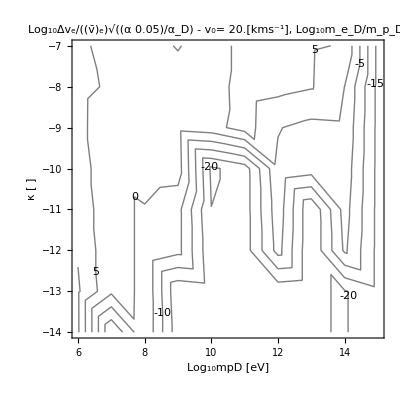

-Graphics-

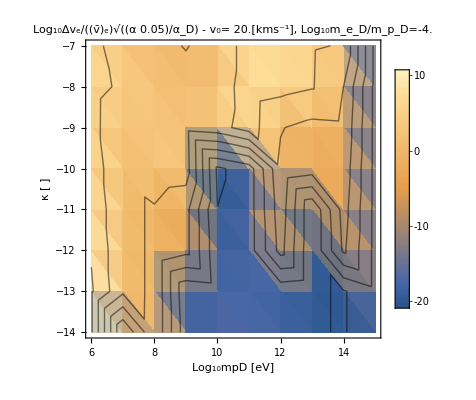

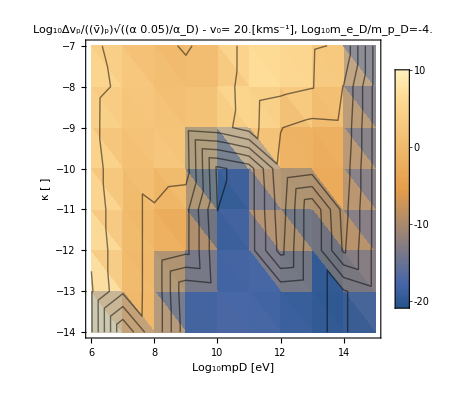

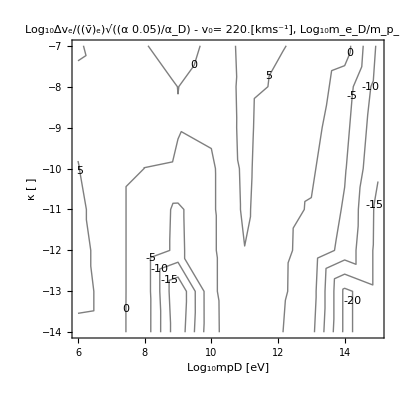

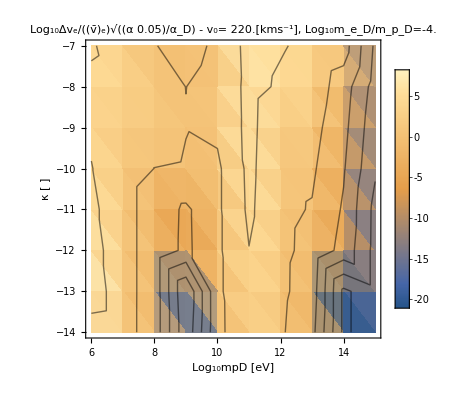

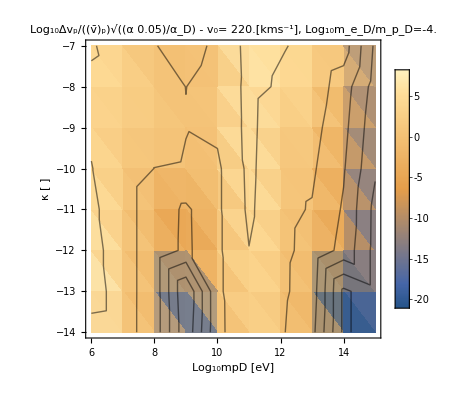

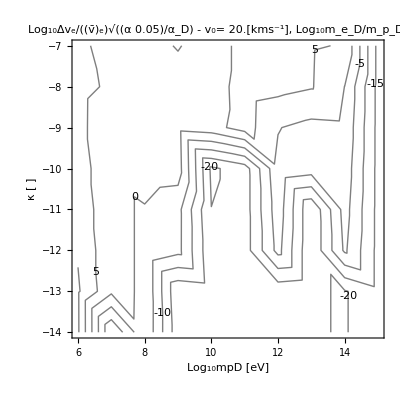

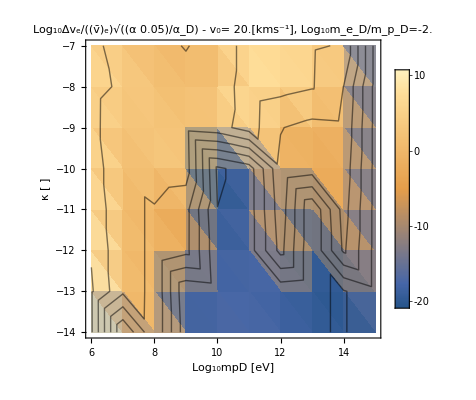

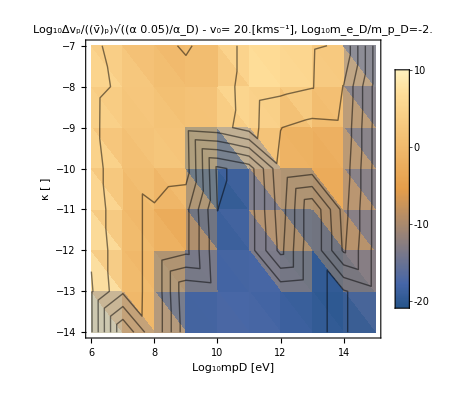

```mathematica
PlotKEchangeκContour[{PDicts1MeVKE,PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

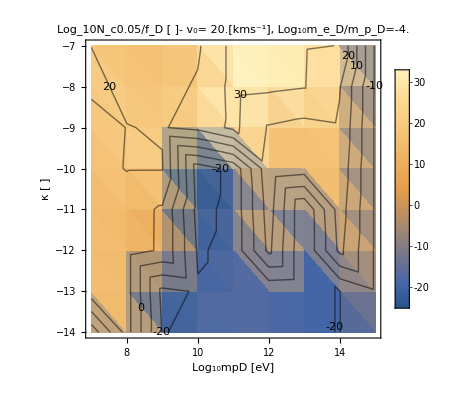

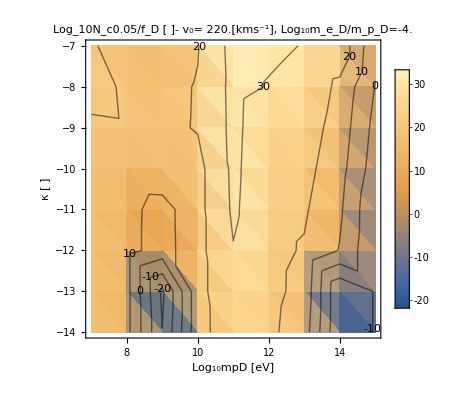

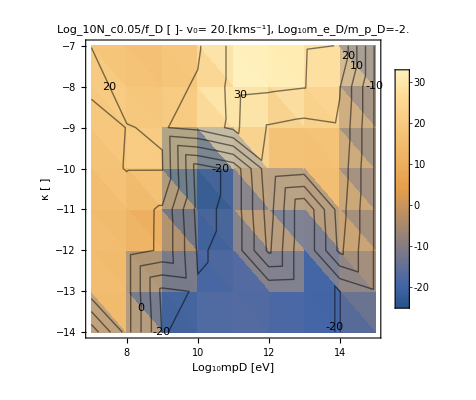

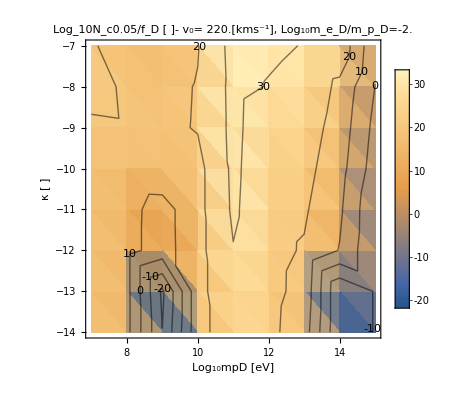

```mathematica
PlotNcκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

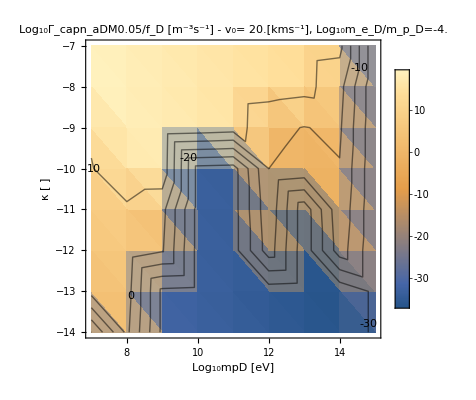

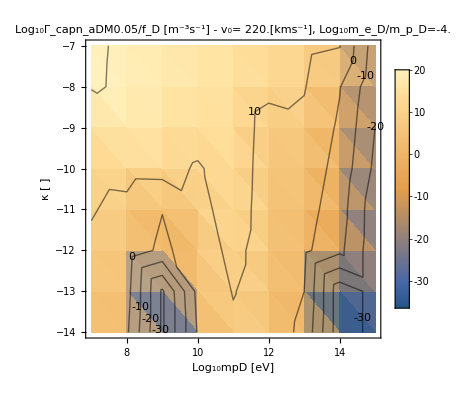

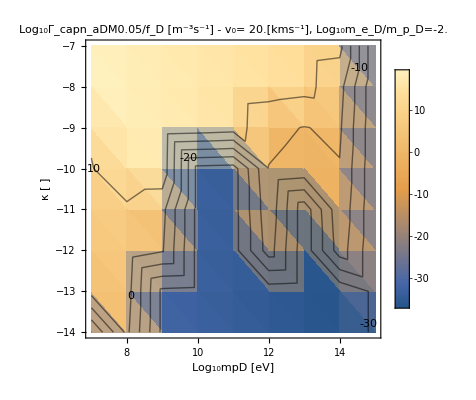

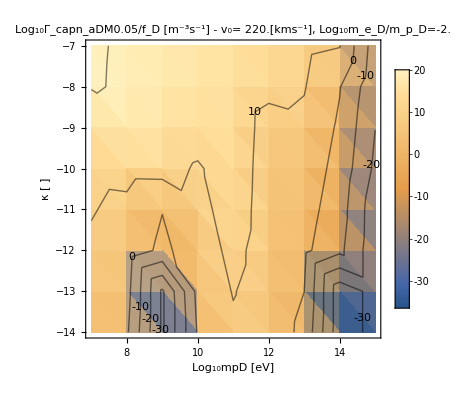

```mathematica
PlotCaptureRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

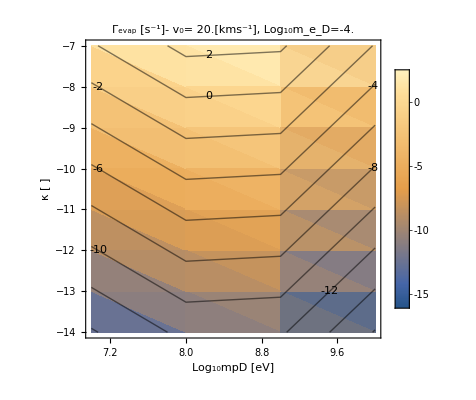

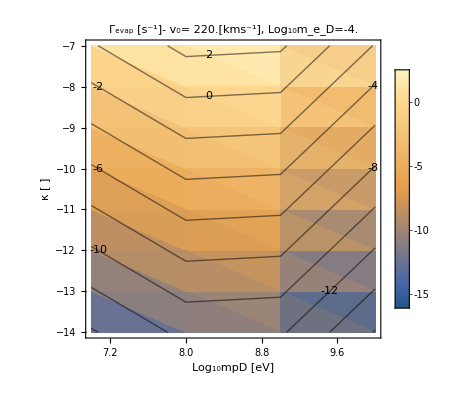

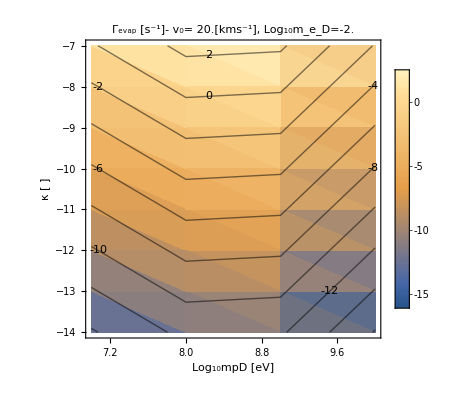

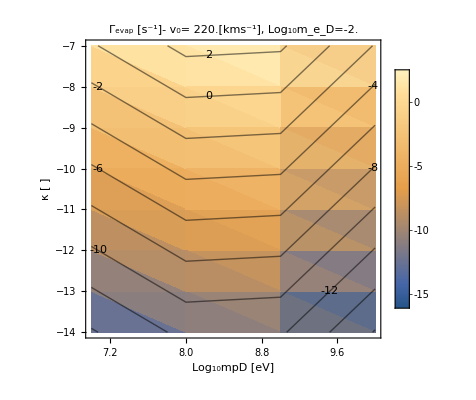

```mathematica
PlotEvaporationRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"Γtotal"/.PDicts10GeVKE
```

{7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11}

#### Soft Scatter Regime

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDict1MeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotPDist[PDict1MeV]
```

1

1

κ is: 1.×10^-14

Memory before 437670328

InterpolatingFunction::dmval: Input value {4.07801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 450685120

κ is: 1.×10^-13

Memory before 450684832

Memory after 452359232

κ is: 1.×10^-12

Memory before 452358976

Memory after 453840752

κ is: 1.×10^-11

Memory before 453840496

Memory after 455223336

κ is: 1.×10^-10

Memory before 455223080

Memory after 456530728

κ is: 1.×10^-9

Memory before 456530472

Memory after 457853680

κ is: 1.×10^-8

Memory before 457853424

Memory after 459152176

κ is: 1.×10^-7

Memory before 459151920

Memory after 459667040

```mathematica
PlotPDist[PDict1MeV]
```

1.×10^6

220000

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

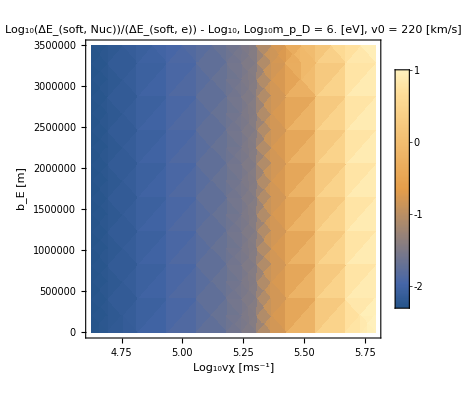

1.×10^6

220000

InterpolatingFunction::dmval: Input value {4.20052} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^6125.98 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^42959.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^6125.98 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

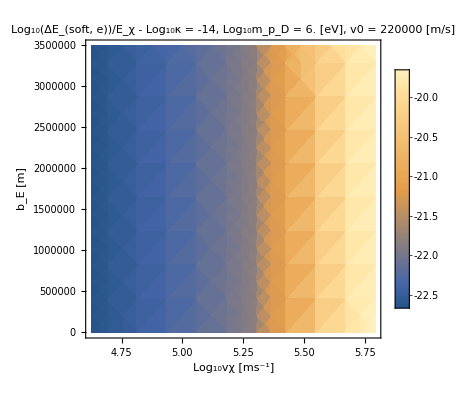

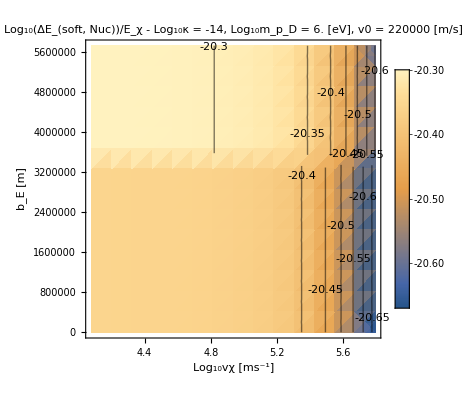

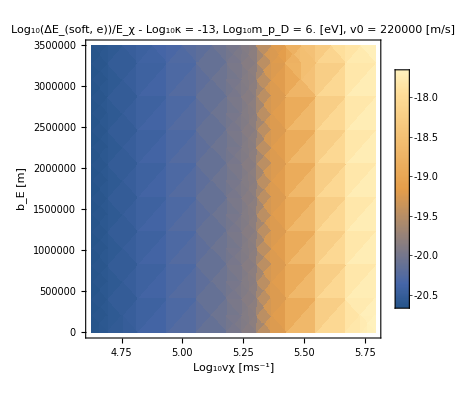

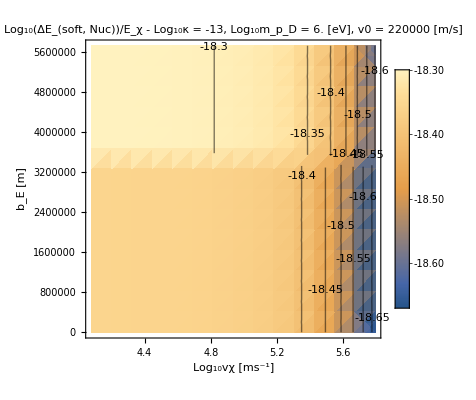

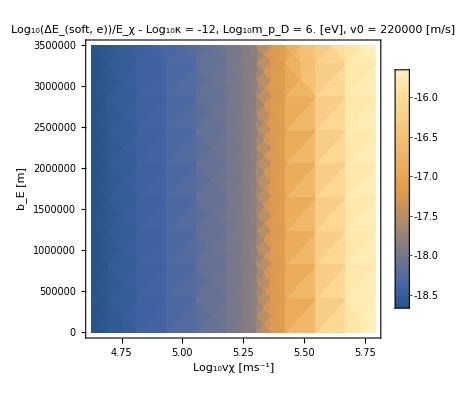

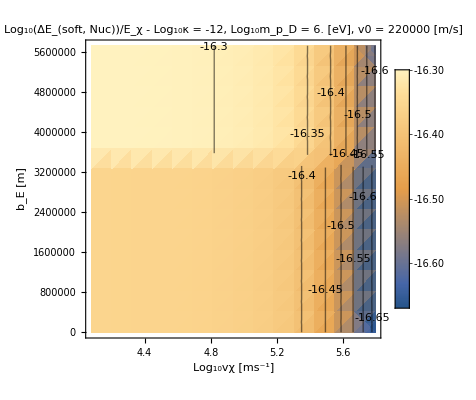

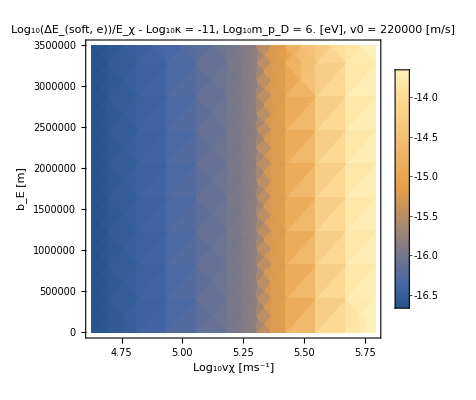

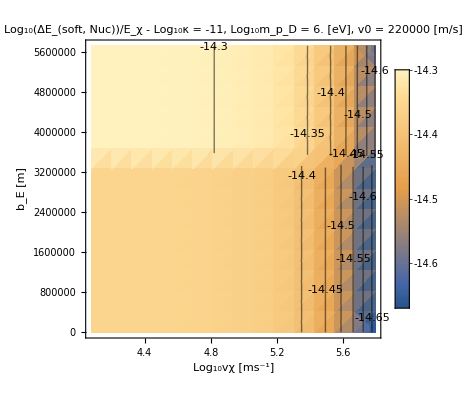

```mathematica
PlotELNucoverE[PDict1MeV,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotELfrac[PDict1MeV,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
```

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDict1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotPDist[PDict1GeV]
```

4

4

κ is: 1.×10^-14

Memory before 684848280

InterpolatingFunction::dmval: Input value {4.07801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^9

220000

InterpolatingFunction::dmval: Input value {-26.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

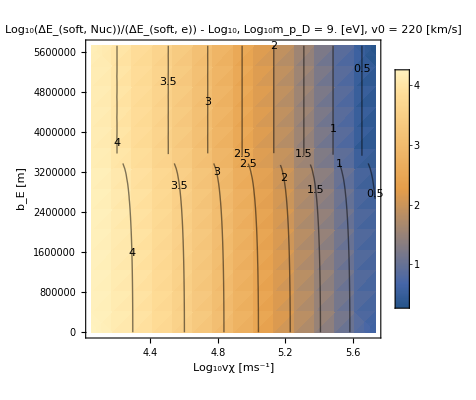

```mathematica
PlotELNucoverE[PDict1GeV]
```

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDict10GeV220=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotPDist[PDict10GeV220]
```

5

5

κ is: 1.×10^-14

Memory before 652145064

InterpolatingFunction::dmval: Input value {4.07801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
PlotELNucoverE[PDict10GeV220]
PlotELNucoverE[PDict10GeV220,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotELfrac[PDict10GeV220,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
```

1.×10^12

220000

InterpolatingFunction::dmval: Input value {-23.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

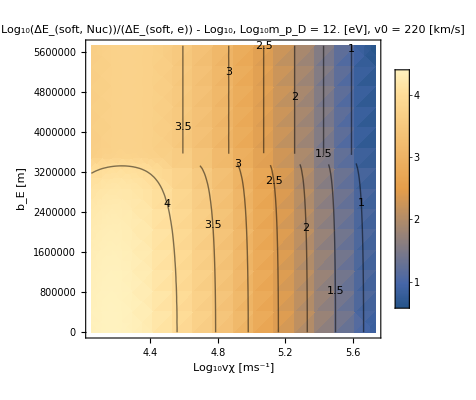

```mathematica
PlotELNucoverE[PDict1TeV]
```

## Scrap

#### Test Plotting to Export only

```mathematica
p1=Show[{Plot[x^2,{x,0,10}],Plot[x^4,{x,0,10}]}];
```

```mathematica
Export[NotebookDirectory[]<>"testplot.png",p1]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot.png

```mathematica
Export[NotebookDirectory[]<>"testplot_1.png",p1]
Export[NotebookDirectory[]<>"testplot_2.png",p1]
Export[NotebookDirectory[]<>"testplot_3.png",p1]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot_1.png

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot_2.png

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot_3.png

```mathematica
DateString[{"Day","_","Month","_","Year"}]
```

07_06_2024

```mathematica
ExportToDir[p1,"testplot.png","testplots"]
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Plots/testplots/testplot_4.png,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Plots/testplots|>

```mathematica
FileExistsQ["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Plots/07_06_2024/testplot.png"]
```

True

#### Unit test Δr

```mathematica
testΔEfunc=("ΔEthroughEarth"/.GetTotalELFunction[ElectronicσDicstallmasses[[3]],NuclearσDicstallmasses[[3]]])
%[10^6,10^4]
```

Quiet[Re[Piecewise[{{dM[#1] dEdlofr$127435[1.1 rc$127435,#2]+dc[#1] dEdlofr$127435[0.9 rc$127435,#2], rc$127435^2>#1^2}, {dM[#1] dEdlofr$127435[1.1 rc$127435,#2], rE$127435^2>#1^2≥rc$127435^2}, {0, True}}]]]&

81.4556

{mpD→1.78×10^-28,mpD→1.78×10^-27,mpD→1.78×10^-26,mpD→1.78×10^-25,mpD→1.78×10^-24}

```mathematica
("mpD" ("c")^2)/("JpereV")/.Constants`SIConstRepl/.mpDPoints[[3]]
```

1.×10^10

```mathematica
κtest = 10^-9;
ΔrTotbyκsquared["mpD"/.mpDPoints[[3]],10^5,10^5,testΔEfunc]
%/κtest^2
```

1.0043×10^-11

1.0043×10^7